```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yuichirotada/Documents/Univ/SLattice/peak_theory

```mathematica
<<init`
```

## Monochromatic

```mathematica
As=5 10^-3;(*10^-2;*)(*3.625 10^-3;*)
```

### direct sampling

```mathematica
npeak=32;
NL=512;
kpeak=2π npeak/NL
σ2=kpeak^2;σ2//N
```

π/8

0.154213

```mathematica
Sqrt[3]/kpeak//N
```

4.41063

```mathematica
Nsim=10;
```

```mathematica
Lpeakdata=Table[Import["data/mono_Lpeak_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_"<>ToString[i]<>".csv"],{i,0,Nsim-1}];
```

```mathematica
HighLdata=Table[Select[Lpeakdata[[i]],#[[4]]>4σ2&],{i,Nsim}];
```

```mathematica
Cpeakdata=Table[Import["data/mono_Cpeak_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_"<>ToString[i]<>".csv"],{i,0,Nsim-1}];
```

```mathematica
HighCdata=Table[Select[Cpeakdata[[i]],#[[5]]>0.45&],{i,Nsim}];
```

```mathematica
matchQ[a_,b_]:=Max[Abs[a[[{1,2,3}]]-b[[{2,3,4}]]]]<=1;
```

```mathematica
onlyInC=Table[Select[HighCdata[[i]],Function[b,!AnyTrue[HighLdata[[i]],matchQ[#,b]&]]],{i,Nsim}]
```

{{},{},{},{},{},{},{},{},{},{}}

```mathematica
Select[HighLdata[[2]],250<#[[1]]<270&]
```

{{251,94,507,0.675894,0.39247},{254,173,394,0.679462,0.393136},{255,323,350,0.620138,0.392765},{256,470,56,0.632658,0.393413},{257,201,460,0.811681,0.392782},{257,469,56,0.629589,0.393758},{264,334,399,0.619223,0.39246},{267,108,504,0.618745,0.392397}}

```mathematica
Select[HighLdata[[4]],175<#[[1]]<195&]
```

{{182,102,387,0.656121,0.393635},{187,318,360,0.632321,0.393152}}

```mathematica
f[x_]=1/2 x(x^2-3)(Erf[1/2 Sqrt[5/2]x]+Erf[Sqrt[5/2]x])+Sqrt[2/(5π)]((8/5+31/4 x^2)Exp[-5/8 x^2]+(-8/5+1/2 x^2)Exp[-5/2 x^2]);
nnu2PT[nu2_]=kpeak^3/(6π)^(3/2) f[nu2] 1/Sqrt[2π] Exp[-nu2^2/2];
```

```mathematica
nudata=Flatten[Lpeakdata[[All,All,4]]/σ2];
nunBins=20;
nubinSpec={Min[nudata],Max[nudata],(Max[nudata]-Min[nudata])/nunBins};
```

```mathematica
nubinEdges=HistogramList[nudata,nubinSpec][[1]];
nubinCenters=MovingAverage[nubinEdges,2];
```

```mathematica
nuPDFPerList=HistogramList[(#[[All,4]])/σ2,nubinSpec,"PDF"][[2]]&/@Lpeakdata;
```

```mathematica
numeanPDF=Mean[nuPDFPerList];
nusePDF=StandardDeviation[nuPDFPerList]/Sqrt[Nsim];
```

```mathematica
nnu2Lat=Table[{nubinCenters[[i]],(numeanPDF[[i]]Length[nudata])/(Nsim NL^3)±(nusePDF[[i]]Length[nudata])/(Nsim NL^3)},{i,nunBins}];
```

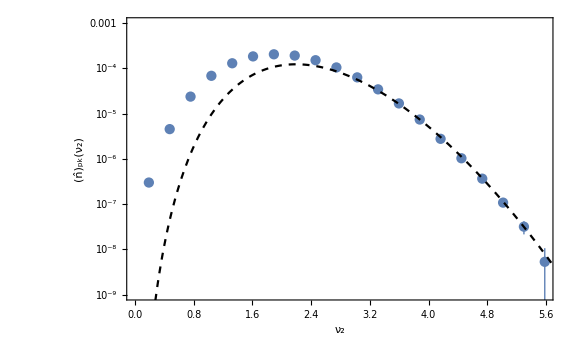

```mathematica
Show[ListLogPlot[nnu2Lat,Joined->False,FrameLabel->{{Subscript[OverHat[n], pk][Subscript[ν, 2]],None},{Subscript[ν, 2],"monochromatic"}},PlotRange->{10^-9,10^-3},PlotLegends->Placed[PointLegend[{"lattice"},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.8,0.8}]],
LogPlot[nnu2PT[nu2],{nu2,0,6},PlotStyle->{Dashed,Black},PlotLegends->Placed[LineLegend[{"peak theory"},LegendMarkerSize->20,LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.8,0.8}]]]
```

```mathematica
Cdata=Flatten[Cpeakdata[[All,All,5]]];
CnBins=20;
CbinSpec={Min[Cdata],Max[Cdata],(Max[Cdata]-Min[Cdata])/CnBins};
```

```mathematica
CbinEdges=HistogramList[Cdata,CbinSpec][[1]];
CbinCenters=MovingAverage[CbinEdges,2];
```

```mathematica
CPDFPerList=HistogramList[#[[All,5]],CbinSpec,"PDF"][[2]]&/@Cpeakdata;
```

```mathematica
CmeanPDF=Mean[CPDFPerList];
CsePDF=StandardDeviation[CPDFPerList]/Sqrt[Nsim];
```

```mathematica
nCLat=Table[{CbinCenters[[i]],(CmeanPDF[[i]]Length[Cdata])/(Nsim NL^3)±(CsePDF[[i]]Length[Cdata])/(Nsim NL^3)},{i,CnBins}];
```

```mathematica
nu2inCm[Cm_]=(Sqrt[1-3/2 Cm]-1)/(c Sqrt[As])/.{c->-1.06};
```

```mathematica
nCpt[Cm_]=nnu2PT[nu2inCm[Cm]]nu2inCm'[Cm];
```

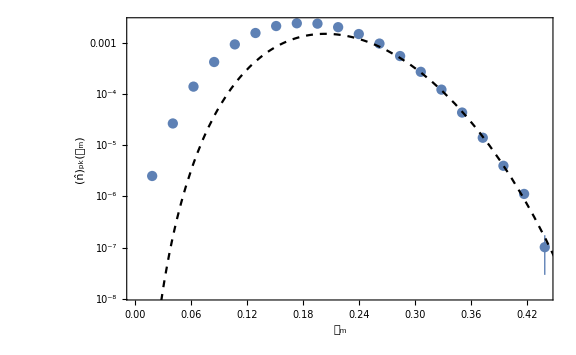

```mathematica
Show[ListLogPlot[nCLat,Joined->False,FrameLabel->{{Subscript[OverHat[n], pk][Subscript[𝒞, "m"]],None},{Subscript[𝒞, "m"],"monochromatic"}},PlotLegends->Placed[PointLegend[{"lattice"},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.6,0.2}]],
LogPlot[nCpt[Cm],{Cm,0,0.6},PlotStyle->{Black,Dashed},PlotLegends->Placed[LineLegend[{"peak theory"},LegendMarkerSize->20,LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.6,0.2}]]]
```

### Importance Sampling

```mathematica
npeak=16;
NL=256;
kpeak=2π npeak/NL
σ2=kpeak^2;σ2//N
```

π/8

0.154213

```mathematica
ISdata=Import["data/mono_muk_"<>ToString[NL]<>"_"<>ToString[npeak]<>".csv"];
Ntot=Length[ISdata]
```

1000

```mathematica
Cmdata=Map[{#[[6]],Log10[Exp[#[[7]]]]}&,ISdata];
```

```mathematica
DensityHistogram[Cmdata,ChartLegends->Automatic,FrameLabel->{Subscript[𝒞, "m"],"log_10𝒲"},GridLines->{{0.533},None}]
```

-Graphics-

```mathematica
Dnu2IS=HistogramList[ISdata[[All,2]]/σ2][[1,2]]-HistogramList[ISdata[[All,2]]/σ2][[1,1]]
```

1/2

```mathematica
nu2minIS=HistogramList[ISdata[[All,2]]/σ2][[1,1]]
nu2maxIS=HistogramList[ISdata[[All,2]]/σ2][[1]]//Last
```

5

12

```mathematica
nu2binning[nu2_]:=Select[ISdata,nu2<=(#[[2]])/σ2<nu2+Dnu2IS&]
k33sum[mu2_]:=Total[(nu2binning[mu2][[All,3]])^3]
```

```mathematica
nSnu2List=Table[{nu2+Dnu2IS/2,k33sum[nu2]/(Ntot Dnu2IS)},{nu2,nu2minIS,nu2maxIS,Dnu2IS}];
```

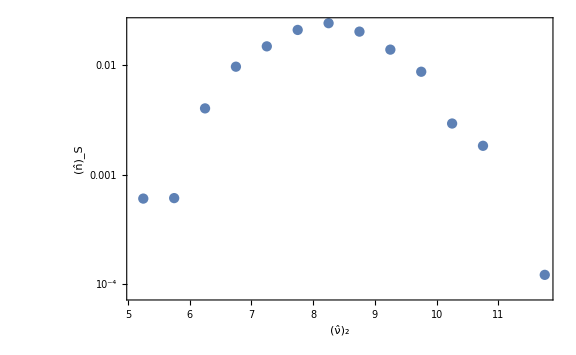

```mathematica
ListLogPlot[nSnu2List,Joined->False,FrameLabel->{Subscript[OverHat[ν], 2],Subscript[OverHat[n], "S"]}]
```

```mathematica
wnu2List=Table[{nu2,If[Length[nu2binning[nu2]]>1,Exp[Mean[nu2binning[nu2][[All,7]]]+Variance[nu2binning[nu2][[All,7]]]/2],0]},{nu2,nu2minIS,nu2maxIS,Dnu2IS}];
wnu2errp=Table[{nu2,If[Length[nu2binning[nu2]]>1,Abs[Exp[Sqrt[Variance[nu2binning[nu2][[All,7]]]/Length[nu2binning[nu2]]+Variance[nu2binning[nu2][[All,7]]]^2/(2Length[nu2binning[nu2]]-2)]]-1],0]},{nu2,nu2minIS,nu2maxIS,Dnu2IS}];
wnu2errm=Table[{nu2,If[Length[nu2binning[nu2]]>1,Abs[Exp[-Sqrt[Variance[nu2binning[nu2][[All,7]]]/Length[nu2binning[nu2]]+Variance[nu2binning[nu2][[All,7]]]^2/(2Length[nu2binning[nu2]]-2)]]-1],0]},{nu2,nu2minIS,nu2maxIS,Dnu2IS}];;
```

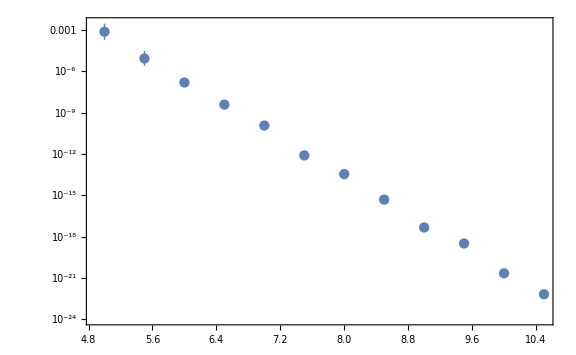

```mathematica
ListLogPlot[Table[{wnu2List[[i,1]],wnu2List[[i,2]]Around[1,{wnu2errm[[i,2]],wnu2errp[[i,2]]}]},{i,Length[wnu2List]}],Joined->False]
```

```mathematica
nTnu2List=Table[{nSnu2List[[i,1]],nSnu2List[[i,2]]wnu2List[[i,2]]Around[1,{wnu2errm[[i,2]],wnu2errp[[i,2]]}]},{i,Length[nSnu2List]}];
```

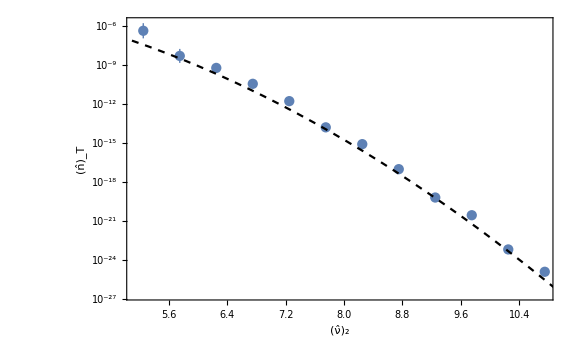

```mathematica
Show[ListLogPlot[nTnu2List,Joined->False,FrameLabel->{Subscript[OverHat[ν], 2],Subscript[OverHat[n], "T"]}],LogPlot[nnu2PT[nu2],{nu2,4,15},PlotStyle->{Black,Dashed}]]
```

```mathematica
padding={{100,10},{70,10}};
```

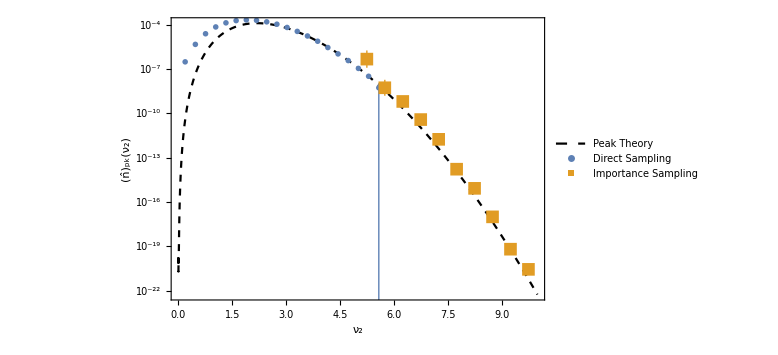

```mathematica
Show[LogPlot[nnu2PT[nu2],{nu2,0,10}(*,PlotRange->{10^-14,10^-2}*),PlotStyle->{Black,Dashed},FrameLabel->{Subscript[ν, 2],Subscript[OverHat[n], pk][Subscript[ν, 2]]},PlotLegends->Placed[LineLegend[{"Peak Theory"},LegendMarkerSize->20,LabelStyle->Directive[Black,Larger,FontFamily->"Palatino"]],{{0.1,0.3},Right}],ImagePadding->padding],
ListLogPlot[nnu2Lat,Joined->False,PlotMarkers->Style["●",Color[1]],PlotLegends->Placed[PointLegend[{"Direct Sampling"},LabelStyle->Directive[Black,Larger,FontFamily->"Palatino"]],{{0.1,0.2},Right}]],
ListLogPlot[nTnu2List,Joined->False,PlotMarkers->Style["■",Color[2],13],IntervalMarkersStyle->Color[2],PlotLegends->Placed[PointLegend[{"Importance Sampling"},LabelStyle->Directive[Black,Larger,FontFamily->"Palatino"]],{{0.1,0.1},Right}]]]
```

```mathematica
DCIS=HistogramList[ISdata[[All,6]]][[1,2]]-HistogramList[ISdata[[All,6]]][[1,1]]
```

1/100

```mathematica
CminIS=HistogramList[ISdata[[All,6]]][[1,1]]
CmaxIS=HistogramList[ISdata[[All,6]]][[1]]//Last
```

41/100

33/50

```mathematica
Cbinning[Cm_]:=Select[ISdata,Cm<=#[[6]]<Cm+DCIS&]
k33sumC[Cm_]:=Total[(Cbinning[Cm][[All,3]])^3]
```

```mathematica
nSCList=Table[{Cm+DCIS/2,k33sumC[Cm]/(Ntot DCIS)},{Cm,CminIS,CmaxIS,DCIS}];
```

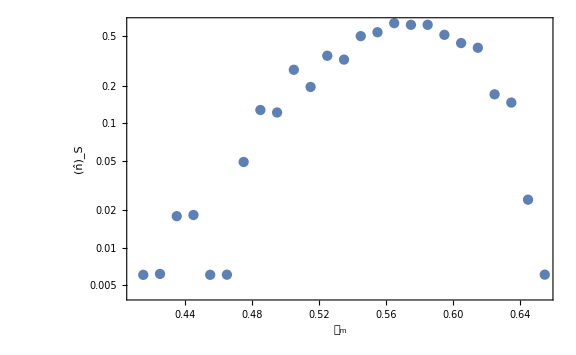

```mathematica
ListLogPlot[nSCList,Joined->False,FrameLabel->{Subscript[𝒞, "m"],Subscript[OverHat[n], "S"]}]
```

```mathematica
wCList=Table[{Cm,If[Length[Cbinning[Cm]]>1,Exp[Mean[Cbinning[Cm][[All,7]]]+Variance[Cbinning[Cm][[All,7]]]/2],0]},{Cm,CminIS,CmaxIS,DCIS}];
wCerrp=Table[{Cm,If[Length[Cbinning[Cm]]>1,Abs[Exp[Sqrt[Variance[Cbinning[Cm][[All,7]]]/Length[Cbinning[Cm]]+Variance[Cbinning[Cm][[All,7]]]^2/(2Length[Cbinning[Cm]]-2)]]-1],0]},{Cm,CminIS,CmaxIS,DCIS}];
wCerrm=Table[{Cm,If[Length[Cbinning[Cm]]>1,Abs[Exp[-Sqrt[Variance[Cbinning[Cm][[All,7]]]/Length[Cbinning[Cm]]+Variance[Cbinning[Cm][[All,7]]]^2/(2Length[Cbinning[Cm]]-2)]]-1],0]},{Cm,CminIS,CmaxIS,DCIS}];
```

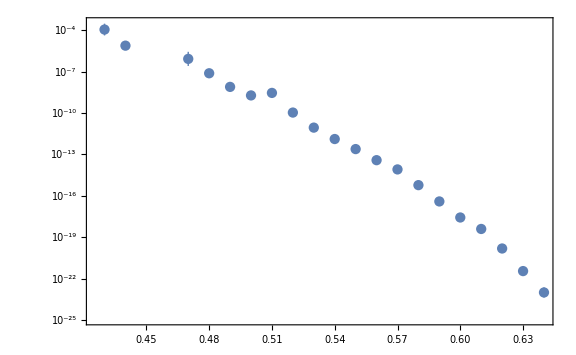

```mathematica
ListLogPlot[Table[{wCList[[i,1]],wCList[[i,2]]Around[1,{wCerrm[[i,2]],wCerrp[[i,2]]}]},{i,Length[wCList]}],Joined->False]
```

```mathematica
nTCList=Table[{nSCList[[i,1]],nSCList[[i,2]]wCList[[i,2]]Around[1,{wCerrm[[i,2]],wCerrp[[i,2]]}]},{i,Length[nSCList]}];
```

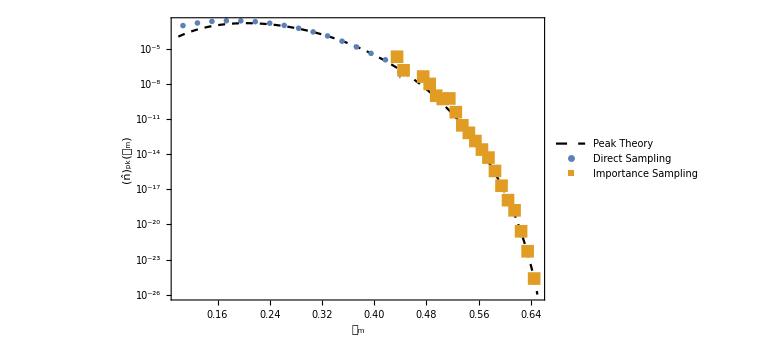

```mathematica
Show[LogPlot[nCpt[Cm],{Cm,0.1,0.65}(*,PlotRange->{10^-15,10^-1}*),PlotStyle->{Black,Dashed},FrameLabel->{Subscript[𝒞, "m"],Subscript[OverHat[n], pk][Subscript[𝒞, "m"]]},PlotLegends->Placed[LineLegend[{"Peak Theory"},LegendMarkerSize->20,LabelStyle->Directive[Black,Larger,FontFamily->"Palatino"]],{{0.1,0.3},Right}],ImagePadding->padding],
ListLogPlot[nCLat,Joined->False,PlotMarkers->Style["●",Color[1]],PlotLegends->Placed[PointLegend[{"Direct Sampling"},LabelStyle->Directive[Black,Larger,FontFamily->"Palatino"]],{{0.1,0.2},Right}]],
ListLogPlot[nTCList,Joined->False,PlotMarkers->Style["■",Color[2],13],IntervalMarkersStyle->Color[2],PlotLegends->Placed[PointLegend[{"Importance Sampling"},LabelStyle->Directive[Black,Larger,FontFamily->"Palatino"]],{{0.1,0.1},Right}]]]
```

## Lognormal σ^2=0.01

```mathematica
npeak=32;
NL=512;
As=10^-2;(*3.625 10^-3;*)
```

```mathematica
kpeak=2π npeak/NL
```

π/8

```mathematica
s2=10^-2;
```

```mathematica
σ1=Sqrt[E^(2 n^2 s2)kpeak^(2n)]/.{n->1};
σ2=Sqrt[E^(2 n^2 s2)kpeak^(2n)]/.{n->2};
σ3=Sqrt[E^(2 n^2 s2)kpeak^(2n)]/.{n->3};
σ4=Sqrt[E^(2 n^2 s2)kpeak^(2n)]/.{n->4};
```

### peak theory

```mathematica
calPz[lnk_]=1/Sqrt[2π s2] Exp[-lnk^2/(2s2)];
```

```mathematica
R3=Sqrt[3] σ3/σ4
```

(8 √3)/(ⅇ^(7/100) π)

```mathematica
γn=E^(-2s2)
```

1/ⅇ^(1/50)

```mathematica
ψ1[x_]:=kpeak^2/σ1^2 NIntegrate[E^(2lnk)calPz[lnk]Sinc[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
ψ2[x_]:=kpeak^4/σ2^2 NIntegrate[E^(4lnk)calPz[lnk]Sinc[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
ψ1p[x_]:=kpeak^2/σ1^2 NIntegrate[E^(3lnk)calPz[lnk]Sinc'[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
ψ2p[x_]:=kpeak^4/σ2^2 NIntegrate[E^(5lnk)calPz[lnk]Sinc'[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
ψ1pp[x_]:=kpeak^2/σ1^2 NIntegrate[E^(4lnk)calPz[lnk]Sinc''[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
ψ2pp[x_]:=kpeak^4/σ2^2 NIntegrate[E^(6lnk)calPz[lnk]Sinc''[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
```

```mathematica
AbsoluteTiming[
ψ1List=ParallelTable[{x,ψ1[x]},{x,10^-2,10,10^-2}];
ψ1pList=ParallelTable[{x,ψ1p[x]},{x,10^-2,10,10^-2}];
ψ1ppList=ParallelTable[{x,ψ1pp[x]},{x,10^-2,10,10^-2}];
ψ2List=ParallelTable[{x,ψ2[x]},{x,10^-2,10,10^-2}];
ψ2pList=ParallelTable[{x,ψ2p[x]},{x,10^-2,10,10^-2}];
ψ2ppList=ParallelTable[{x,ψ2pp[x]},{x,10^-2,10,10^-2}];]
```

{10.1575,Null}

```mathematica
ψ1int[x_]=Interpolation[ψ1List][x];
ψ1pint[x_]=Interpolation[ψ1pList][x];
ψ1ppint[x_]=Interpolation[ψ1ppList][x];
ψ2int[x_]=Interpolation[ψ2List][x];
ψ2pint[x_]=Interpolation[ψ2pList][x];
ψ2ppint[x_]=Interpolation[ψ2ppList][x];
```

```mathematica
ζx[x_,k3t_]=(1/(1-γn^2)(ψ1int[x]-1/3 R3^2 σ2^2/σ1^2 ψ2int[x])-k3t^2/(γn(1-γn^2))(γn^2 ψ1int[x]-1/3 R3^2 σ2^2/σ1^2 ψ2int[x]));
ζp[x_,k3t_]=(1/(1-γn^2)(ψ1pint[x]-1/3 R3^2 σ2^2/σ1^2 ψ2pint[x])-k3t^2/(γn(1-γn^2))(γn^2 ψ1pint[x]-1/3 R3^2 σ2^2/σ1^2 ψ2pint[x]));
ζpp[x_,k3t_]=(1/(1-γn^2)(ψ1ppint[x]-1/3 R3^2 σ2^2/σ1^2 ψ2ppint[x])-k3t^2/(γn(1-γn^2))(γn^2 ψ1ppint[x]-1/3 R3^2 σ2^2/σ1^2 ψ2ppint[x]));
```

```mathematica
CmCond[x_,k3t_]=(ζp[x,k3t]+x ζpp[x,k3t])/x^3;
```

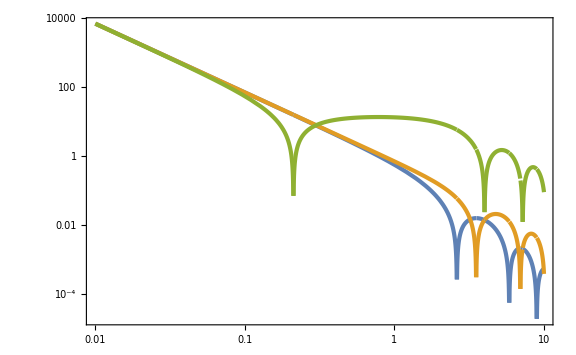

```mathematica
LogLogPlot[{Abs[CmCond[x,1]],Abs[CmCond[x,10^-2]],Abs[CmCond[x,10]]},{x,10^-2,10}]
```

```mathematica
xmList=ParallelTable[{10^lnk3t,x/.FindRoot[CmCond[x,10^lnk3t]==0,{x,Min[1/(2 10^lnk3t),1]},WorkingPrecision->30]//Quiet},{lnk3t,-2,2,10^-2}];
```

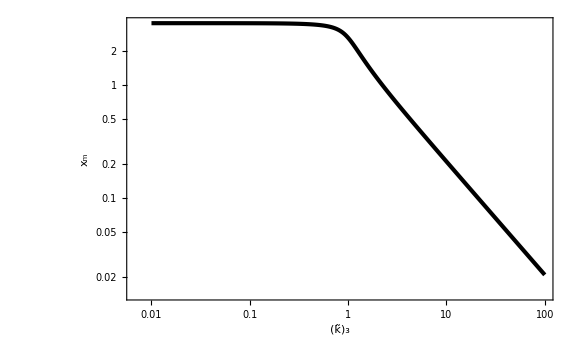

```mathematica
ListLogLogPlot[xmList,PlotRange->Full,FrameLabel->{Subscript[OverTilde[k], 3],Subscript[x, "m"]},PlotStyle->{Black,AbsoluteThickness[3]}]
```

```mathematica
xmint[k3t_]=Interpolation[xmList][k3t];
```

```mathematica
nu2inCk[Cm_,k3t_]=(Sqrt[1-3/2 Cm]-1)/(xmint[k3t] σ1^2/σ2 Sqrt[As]ζp[xmint[k3t],k3t]);
dnu2dCm[Cm_,k3t_]=D[nu2inCk[Cm,k3t], Cm]//Simplify;
```

```mathematica
f[x_]=1/2 x(x^2-3)(Erf[1/2 Sqrt[5/2]x]+Erf[Sqrt[5/2]x])+Sqrt[2/(5π)]((8/5+31/4 x^2)Exp[-5/8 x^2]+(-8/5+1/2 x^2)Exp[-5/2 x^2]);
P13[ν_,ξ_]=1/(2π Sqrt[1-γn^2])Exp[-1/2(ν^2+(ξ-γn ν)^2/(1-γn^2))];
npkPT[nu2_,k3t_]=2/(6π)^(3/2)(σ4/σ3)^3 nu2 k3t f[nu2 k3t^2]P13[nu2,nu2 k3t^2];
```

```mathematica
nCpt[Cm_]:=NIntegrate[npkPT[nu2inCk[Cm,k3t],k3t]Abs[dnu2dCm[Cm,k3t]],{k3t,5/10,3/2}(*,WorkingPrecision->30,MaxRecursion->12*)]
```

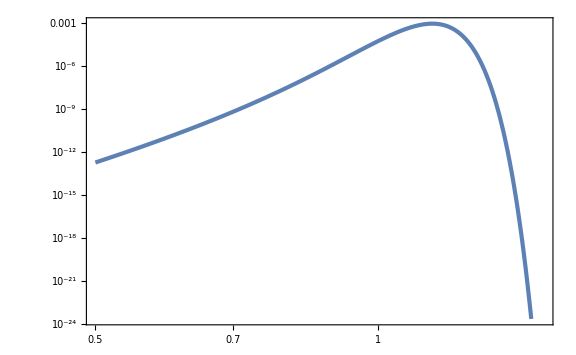

```mathematica
LogLogPlot[npkPT[nu2inCk[Cm,k3t],k3t]Abs[dnu2dCm[Cm,k3t]]/.{Cm->1/10},{k3t,5/10,3/2},WorkingPrecision->30]
```

```mathematica
nCptList=ParallelTable[{Cm,nCpt[Cm]},{Cm,10^-1,6/10,10^-2}];//AbsoluteTiming
```

{117.274,Null}

```mathematica
nCptint[Cm_]=Interpolation[nCptList][Cm];
```

### direct sampling

```mathematica
Nsim=10;
```

```mathematica
Lpeakdata=Table[Import["data/LN_Lpeak_0,01_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_"<>ToString[i]<>".csv"],{i,0,Nsim-1}];
```

```mathematica
HighLdata=Table[Select[Lpeakdata[[i]],#[[4]]>4σ2&],{i,Nsim}];
```

```mathematica
Cpeakdata=Table[Import["data/LN_Cpeak_0,01_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_"<>ToString[i]<>".csv"],{i,0,Nsim-1}];
```

```mathematica
HighCdata=Table[Select[Cpeakdata[[i]],#[[5]]>0.45&],{i,Nsim}];
```

```mathematica
matchQ[a_,b_]:=Max[Abs[a[[{1,2,3}]]-b[[{2,3,4}]]]]<=1;
```

```mathematica
onlyInC=Table[Select[HighCdata[[i]],Function[b,!AnyTrue[HighLdata[[i]],matchQ[#,b]&]]],{i,Nsim}];
```

```mathematica
γ3=σ3^2/(σ2 σ4);
f[x_]=1/2 x(x^2-3)(Erf[1/2 Sqrt[5/2]x]+Erf[Sqrt[5/2]x])+Sqrt[2/(5π)]((8/5+31/4 x^2)Exp[-5/8 x^2]+(-8/5+1/2 x^2)Exp[-5/2 x^2]);
P13[ν_,ξ_]=1/(2π Sqrt[1-γ3^2])Exp[-1/2(ν^2+(ξ-γ3 ν)^2/(1-γ3^2))];
npkPT[nu2_,k3t_]=2/(6π)^(3/2)σ4^3/σ3^3 nu2 k3t f[nu2 k3t^2]P13[nu2,nu2 k3t^2];
nnu2PT[nu2_]:=NIntegrate[npkPT[nu2,k3t],{k3t,0,∞}];
```

```mathematica
nudata=Flatten[Lpeakdata[[All,All,4]]/σ2];
nunBins=20;
nubinSpec={Min[nudata],Max[nudata],(Max[nudata]-Min[nudata])/nunBins};
```

```mathematica
nubinEdges=HistogramList[nudata,nubinSpec][[1]];
nubinCenters=MovingAverage[nubinEdges,2];
```

```mathematica
nuPDFPerList=HistogramList[(#[[All,4]])/σ2,nubinSpec,"PDF"][[2]]&/@Lpeakdata;
```

```mathematica
numeanPDF=Mean[nuPDFPerList];
nusePDF=StandardDeviation[nuPDFPerList]/Sqrt[Nsim];
```

```mathematica
nnu2Lat=Table[{nubinCenters[[i]],(numeanPDF[[i]]Length[nudata])/(Nsim NL^3)±(nusePDF[[i]]Length[nudata])/(Nsim NL^3)},{i,nunBins}];
```

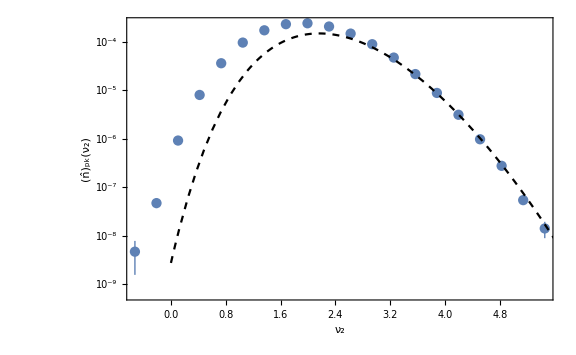

```mathematica
Show[ListLogPlot[nnu2Lat,Joined->False,FrameLabel->{{Subscript[OverHat[n], pk][Subscript[ν, 2]],None},{Subscript[ν, 2],σ^2==N[s2]}}(*,PlotRange->{10^-9,10^-3}*),PlotLegends->Placed[PointLegend[{"lattice"},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.6,0.2}]],LogPlot[nnu2PT[nu2],{nu2,0,6},PlotStyle->{Dashed,Black},PlotLegends->Placed[LineLegend[{"peak theory"},LegendMarkerSize->20,LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.6,0.2}]]]
```

```mathematica
Cdata=Flatten[Cpeakdata[[All,All,5]]];
CnBins=20;
CbinSpec={Min[Cdata],Max[Cdata],(Max[Cdata]-Min[Cdata])/CnBins};
```

```mathematica
CbinEdges=HistogramList[Cdata,CbinSpec][[1]];
CbinCenters=MovingAverage[CbinEdges,2];
```

```mathematica
CPDFPerList=HistogramList[#[[All,5]],CbinSpec,"PDF"][[2]]&/@Cpeakdata;
```

```mathematica
CmeanPDF=Mean[CPDFPerList];
CsePDF=StandardDeviation[CPDFPerList]/Sqrt[Nsim];
```

```mathematica
nCLat=Table[{CbinCenters[[i]],(CmeanPDF[[i]]Length[Cdata])/(Nsim NL^3)±(CsePDF[[i]]Length[Cdata])/(Nsim NL^3)},{i,CnBins}];
```

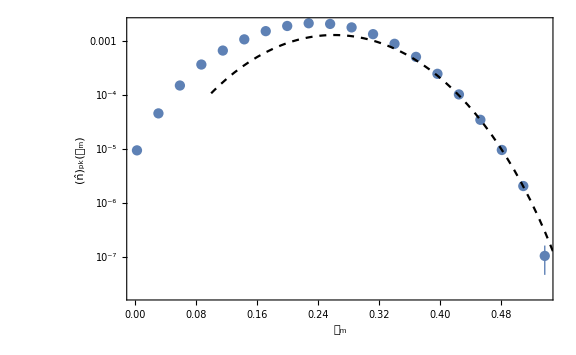

```mathematica
Show[ListLogPlot[nCLat,Joined->False,FrameLabel->{{Subscript[OverHat[n], pk][Subscript[𝒞, "m"]],None},{Subscript[𝒞, "m"],σ^2==N[s2]}},PlotLegends->Placed[PointLegend[{"lattice"},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.6,0.2}]],
LogPlot[nCptint[Cm],{Cm,0.1,0.6},PlotStyle->{Black,Dashed},PlotLegends->Placed[LineLegend[{"peak theory"},LegendMarkerSize->20,LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.6,0.2}]]]
```

## Lognormal σ^2=0.03

```mathematica
npeak=32;
NL=512;
As=10^-2;(*3.625 10^-3;*)
```

```mathematica
kpeak=2π npeak/NL
```

π/8

```mathematica
s2=3/100;
```

```mathematica
σ1=Sqrt[E^(2 n^2 s2)kpeak^(2n)]/.{n->1};
σ2=Sqrt[E^(2 n^2 s2)kpeak^(2n)]/.{n->2};
σ3=Sqrt[E^(2 n^2 s2)kpeak^(2n)]/.{n->3};
σ4=Sqrt[E^(2 n^2 s2)kpeak^(2n)]/.{n->4};
```

### peak theory

```mathematica
calPz[lnk_]=1/Sqrt[2π s2] Exp[-lnk^2/(2s2)];
```

```mathematica
R3=Sqrt[3] σ3/σ4
```

(8 √3)/(ⅇ^(21/100) π)

```mathematica
γn=E^(-2s2)
```

1/ⅇ^(3/50)

```mathematica
ψ1[x_]:=kpeak^2/σ1^2 NIntegrate[E^(2lnk)calPz[lnk]Sinc[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
ψ2[x_]:=kpeak^4/σ2^2 NIntegrate[E^(4lnk)calPz[lnk]Sinc[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
ψ1p[x_]:=kpeak^2/σ1^2 NIntegrate[E^(3lnk)calPz[lnk]Sinc'[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
ψ2p[x_]:=kpeak^4/σ2^2 NIntegrate[E^(5lnk)calPz[lnk]Sinc'[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
ψ1pp[x_]:=kpeak^2/σ1^2 NIntegrate[E^(4lnk)calPz[lnk]Sinc''[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
ψ2pp[x_]:=kpeak^4/σ2^2 NIntegrate[E^(6lnk)calPz[lnk]Sinc''[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
```

```mathematica
AbsoluteTiming[
ψ1List=ParallelTable[{x,ψ1[x]},{x,10^-2,10,10^-2}];
ψ1pList=ParallelTable[{x,ψ1p[x]},{x,10^-2,10,10^-2}];
ψ1ppList=ParallelTable[{x,ψ1pp[x]},{x,10^-2,10,10^-2}];
ψ2List=ParallelTable[{x,ψ2[x]},{x,10^-2,10,10^-2}];
ψ2pList=ParallelTable[{x,ψ2p[x]},{x,10^-2,10,10^-2}];
ψ2ppList=ParallelTable[{x,ψ2pp[x]},{x,10^-2,10,10^-2}];]
```

{13.5043,Null}

```mathematica
ψ1int[x_]=Interpolation[ψ1List][x];
ψ1pint[x_]=Interpolation[ψ1pList][x];
ψ1ppint[x_]=Interpolation[ψ1ppList][x];
ψ2int[x_]=Interpolation[ψ2List][x];
ψ2pint[x_]=Interpolation[ψ2pList][x];
ψ2ppint[x_]=Interpolation[ψ2ppList][x];
```

```mathematica
ζx[x_,k3t_]=(1/(1-γn^2)(ψ1int[x]-1/3 R3^2 σ2^2/σ1^2 ψ2int[x])-k3t^2/(γn(1-γn^2))(γn^2 ψ1int[x]-1/3 R3^2 σ2^2/σ1^2 ψ2int[x]));
ζp[x_,k3t_]=(1/(1-γn^2)(ψ1pint[x]-1/3 R3^2 σ2^2/σ1^2 ψ2pint[x])-k3t^2/(γn(1-γn^2))(γn^2 ψ1pint[x]-1/3 R3^2 σ2^2/σ1^2 ψ2pint[x]));
ζpp[x_,k3t_]=(1/(1-γn^2)(ψ1ppint[x]-1/3 R3^2 σ2^2/σ1^2 ψ2ppint[x])-k3t^2/(γn(1-γn^2))(γn^2 ψ1ppint[x]-1/3 R3^2 σ2^2/σ1^2 ψ2ppint[x]));
```

```mathematica
CmCond[x_,k3t_]=(ζp[x,k3t]+x ζpp[x,k3t])/x^3;
```

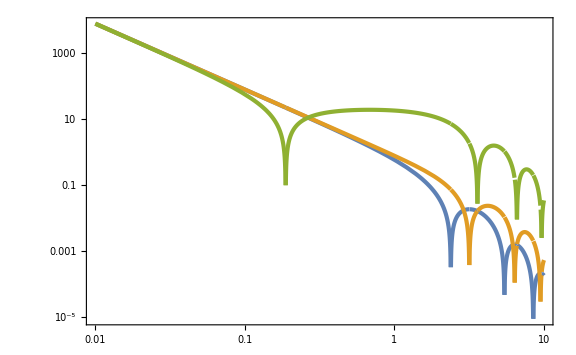

```mathematica
LogLogPlot[{Abs[CmCond[x,1]],Abs[CmCond[x,10^-2]],Abs[CmCond[x,10]]},{x,10^-2,10}]
```

```mathematica
xmList=ParallelTable[{10^lnk3t,x/.FindRoot[CmCond[x,10^lnk3t]==0,{x,Min[1/(2 10^lnk3t),1]},WorkingPrecision->30]//Quiet},{lnk3t,-2,2,10^-2}];
```

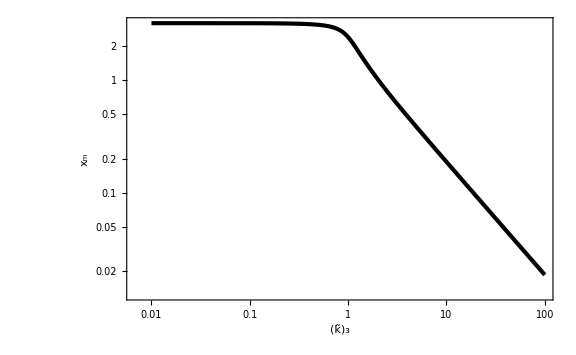

```mathematica
ListLogLogPlot[xmList,PlotRange->Full,FrameLabel->{Subscript[OverTilde[k], 3],Subscript[x, "m"]},PlotStyle->{Black,AbsoluteThickness[3]}]
```

```mathematica
xmint[k3t_]=Interpolation[xmList][k3t];
```

```mathematica
nu2inCk[Cm_,k3t_]=(Sqrt[1-3/2 Cm]-1)/(xmint[k3t] σ1^2/σ2 Sqrt[As]ζp[xmint[k3t],k3t]);
dnu2dCm[Cm_,k3t_]=D[nu2inCk[Cm,k3t], Cm]//Simplify;
```

```mathematica
f[x_]=1/2 x(x^2-3)(Erf[1/2 Sqrt[5/2]x]+Erf[Sqrt[5/2]x])+Sqrt[2/(5π)]((8/5+31/4 x^2)Exp[-5/8 x^2]+(-8/5+1/2 x^2)Exp[-5/2 x^2]);
P13[ν_,ξ_]=1/(2π Sqrt[1-γn^2])Exp[-1/2(ν^2+(ξ-γn ν)^2/(1-γn^2))];
npkPT[nu2_,k3t_]=2/(6π)^(3/2)(σ4/σ3)^3 nu2 k3t f[nu2 k3t^2]P13[nu2,nu2 k3t^2];
```

```mathematica
nCpt[Cm_]:=NIntegrate[npkPT[nu2inCk[Cm,k3t],k3t]Abs[dnu2dCm[Cm,k3t]],{k3t,5/10,3/2}(*,WorkingPrecision->30,MaxRecursion->12*)]
```

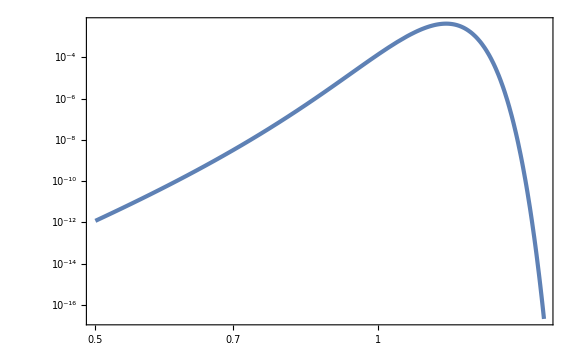

```mathematica
LogLogPlot[npkPT[nu2inCk[Cm,k3t],k3t]Abs[dnu2dCm[Cm,k3t]]/.{Cm->1/10},{k3t,5/10,3/2},WorkingPrecision->30]
```

```mathematica
nCptList=ParallelTable[{Cm,nCpt[Cm]},{Cm,10^-1,6/10,10^-2}];//AbsoluteTiming
```

{123.009,Null}

```mathematica
nCptint[Cm_]=Interpolation[nCptList][Cm];
```

### direct sampling

```mathematica
Nsim=1;
```

```mathematica
Lpeakdata=Table[Import["data/LN_Lpeak_0,03_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_"<>ToString[i]<>".csv"],{i,0,Nsim-1}];
```

```mathematica
HighLdata=Table[Select[Lpeakdata[[i]],#[[4]]>4σ2&],{i,Nsim}];
```

```mathematica
Cpeakdata=Table[Import["data/LN_Cpeak_0,03_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_"<>ToString[i]<>".csv"],{i,0,Nsim-1}];
```

```mathematica
HighCdata=Table[Select[Cpeakdata[[i]],#[[5]]>0.45&],{i,Nsim}];
```

```mathematica
matchQ[a_,b_]:=Max[Abs[a[[{1,2,3}]]-b[[{2,3,4}]]]]<=1;
```

```mathematica
onlyInC=Table[Select[HighCdata[[i]],Function[b,!AnyTrue[HighLdata[[i]],matchQ[#,b]&]]],{i,Nsim}];
```

```mathematica
γ3=σ3^2/(σ2 σ4);
f[x_]=1/2 x(x^2-3)(Erf[1/2 Sqrt[5/2]x]+Erf[Sqrt[5/2]x])+Sqrt[2/(5π)]((8/5+31/4 x^2)Exp[-5/8 x^2]+(-8/5+1/2 x^2)Exp[-5/2 x^2]);
P13[ν_,ξ_]=1/(2π Sqrt[1-γ3^2])Exp[-1/2(ν^2+(ξ-γ3 ν)^2/(1-γ3^2))];
npkPT[nu2_,k3t_]=2/(6π)^(3/2)σ4^3/σ3^3 nu2 k3t f[nu2 k3t^2]P13[nu2,nu2 k3t^2];
nnu2PT[nu2_]:=NIntegrate[npkPT[nu2,k3t],{k3t,0,∞}];
```

```mathematica
nudata=Flatten[Lpeakdata[[All,All,4]]/σ2];
nunBins=20;
nubinSpec={Min[nudata],Max[nudata],(Max[nudata]-Min[nudata])/nunBins};
```

```mathematica
nubinEdges=HistogramList[nudata,nubinSpec][[1]];
nubinCenters=MovingAverage[nubinEdges,2];
```

```mathematica
nuPDFPerList=HistogramList[(#[[All,4]])/σ2,nubinSpec,"PDF"][[2]]&/@Lpeakdata;
```

```mathematica
numeanPDF=Mean[nuPDFPerList];
(*nusePDF=StandardDeviation[nuPDFPerList]/Sqrt[Nsim];*)
```

```mathematica
nnu2Lat=Table[{nubinCenters[[i]],(numeanPDF[[i]]Length[nudata])/(Nsim NL^3)(*±(nusePDF[[i]]Length[nudata])/(Nsim NL^3)*)},{i,nunBins}];
```

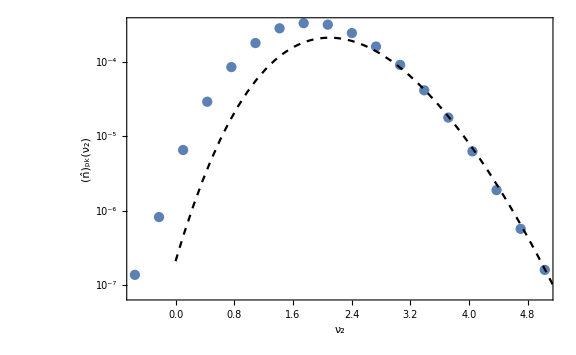

```mathematica
Show[ListLogPlot[nnu2Lat,Joined->False,FrameLabel->{{Subscript[OverHat[n], pk][Subscript[ν, 2]],None},{Subscript[ν, 2],σ^2==N[s2]}}(*,PlotRange->{10^-9,10^-3}*),PlotLegends->Placed[PointLegend[{"lattice"},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.6,0.2}]],LogPlot[nnu2PT[nu2],{nu2,0,6},PlotStyle->{Dashed,Black},PlotLegends->Placed[LineLegend[{"peak theory"},LegendMarkerSize->20,LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.6,0.2}]]]
```

```mathematica
Cdata=Flatten[Cpeakdata[[All,All,5]]];
CnBins=20;
CbinSpec={Min[Cdata],Max[Cdata],(Max[Cdata]-Min[Cdata])/CnBins};
```

```mathematica
CbinEdges=HistogramList[Cdata,CbinSpec][[1]];
CbinCenters=MovingAverage[CbinEdges,2];
```

```mathematica
CPDFPerList=HistogramList[#[[All,5]],CbinSpec,"PDF"][[2]]&/@Cpeakdata;
```

```mathematica
CmeanPDF=Mean[CPDFPerList];
(*CsePDF=StandardDeviation[CPDFPerList]/Sqrt[Nsim];*)
```

```mathematica
nCLat=Table[{CbinCenters[[i]],(CmeanPDF[[i]]Length[Cdata])/(Nsim NL^3)(*±(CsePDF[[i]]Length[Cdata])/(Nsim NL^3)*)},{i,CnBins}];
```

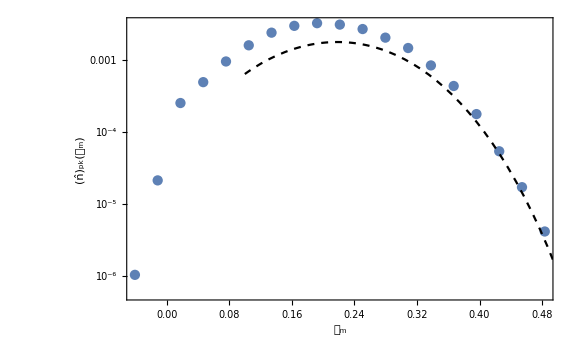

```mathematica
Show[ListLogPlot[nCLat,Joined->False,FrameLabel->{{Subscript[OverHat[n], pk][Subscript[𝒞, "m"]],None},{Subscript[𝒞, "m"],σ^2==N[s2]}},PlotLegends->Placed[PointLegend[{"lattice"},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.6,0.2}]],
LogPlot[nCptint[Cm],{Cm,0.1,0.6},PlotStyle->{Black,Dashed},PlotLegends->Placed[LineLegend[{"peak theory"},LegendMarkerSize->20,LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.6,0.2}]]]
```

## Lognormal σ^2=0.05

```mathematica
npeak=32;
NL=512;
As=10^-2;(*3.625 10^-3;*)
```

```mathematica
kpeak=2π npeak/NL
```

π/8

```mathematica
s2=5/100;
```

```mathematica
σ1=Sqrt[E^(2 n^2 s2)kpeak^(2n)]/.{n->1};
σ2=Sqrt[E^(2 n^2 s2)kpeak^(2n)]/.{n->2};
σ3=Sqrt[E^(2 n^2 s2)kpeak^(2n)]/.{n->3};
σ4=Sqrt[E^(2 n^2 s2)kpeak^(2n)]/.{n->4};
```

### peak theory

```mathematica
calPz[lnk_]=1/Sqrt[2π s2] Exp[-lnk^2/(2s2)];
```

```mathematica
R3=Sqrt[3] σ3/σ4
```

(8 √3)/(ⅇ^(7/20) π)

```mathematica
γn=E^(-2s2)
```

1/ⅇ^(1/10)

```mathematica
ψ1[x_]:=kpeak^2/σ1^2 NIntegrate[E^(2lnk)calPz[lnk]Sinc[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
ψ2[x_]:=kpeak^4/σ2^2 NIntegrate[E^(4lnk)calPz[lnk]Sinc[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
ψ1p[x_]:=kpeak^2/σ1^2 NIntegrate[E^(3lnk)calPz[lnk]Sinc'[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
ψ2p[x_]:=kpeak^4/σ2^2 NIntegrate[E^(5lnk)calPz[lnk]Sinc'[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
ψ1pp[x_]:=kpeak^2/σ1^2 NIntegrate[E^(4lnk)calPz[lnk]Sinc''[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
ψ2pp[x_]:=kpeak^4/σ2^2 NIntegrate[E^(6lnk)calPz[lnk]Sinc''[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
```

```mathematica
AbsoluteTiming[
ψ1List=ParallelTable[{x,ψ1[x]},{x,10^-2,10,10^-2}];
ψ1pList=ParallelTable[{x,ψ1p[x]},{x,10^-2,10,10^-2}];
ψ1ppList=ParallelTable[{x,ψ1pp[x]},{x,10^-2,10,10^-2}];
ψ2List=ParallelTable[{x,ψ2[x]},{x,10^-2,10,10^-2}];
ψ2pList=ParallelTable[{x,ψ2p[x]},{x,10^-2,10,10^-2}];
ψ2ppList=ParallelTable[{x,ψ2pp[x]},{x,10^-2,10,10^-2}];]
```

{14.7274,Null}

```mathematica
ψ1int[x_]=Interpolation[ψ1List][x];
ψ1pint[x_]=Interpolation[ψ1pList][x];
ψ1ppint[x_]=Interpolation[ψ1ppList][x];
ψ2int[x_]=Interpolation[ψ2List][x];
ψ2pint[x_]=Interpolation[ψ2pList][x];
ψ2ppint[x_]=Interpolation[ψ2ppList][x];
```

```mathematica
ζx[x_,k3t_]=(1/(1-γn^2)(ψ1int[x]-1/3 R3^2 σ2^2/σ1^2 ψ2int[x])-k3t^2/(γn(1-γn^2))(γn^2 ψ1int[x]-1/3 R3^2 σ2^2/σ1^2 ψ2int[x]));
ζp[x_,k3t_]=(1/(1-γn^2)(ψ1pint[x]-1/3 R3^2 σ2^2/σ1^2 ψ2pint[x])-k3t^2/(γn(1-γn^2))(γn^2 ψ1pint[x]-1/3 R3^2 σ2^2/σ1^2 ψ2pint[x]));
ζpp[x_,k3t_]=(1/(1-γn^2)(ψ1ppint[x]-1/3 R3^2 σ2^2/σ1^2 ψ2ppint[x])-k3t^2/(γn(1-γn^2))(γn^2 ψ1ppint[x]-1/3 R3^2 σ2^2/σ1^2 ψ2ppint[x]));
```

```mathematica
CmCond[x_,k3t_]=(ζp[x,k3t]+x ζpp[x,k3t])/x^3;
```

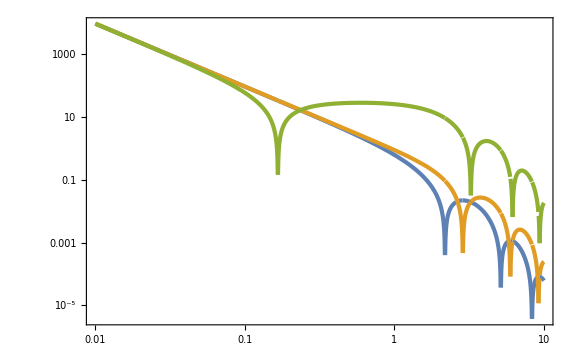

```mathematica
LogLogPlot[{Abs[CmCond[x,1]],Abs[CmCond[x,10^-2]],Abs[CmCond[x,10]]},{x,10^-2,10}]
```

```mathematica
xmList=ParallelTable[{10^lnk3t,x/.FindRoot[CmCond[x,10^lnk3t]==0,{x,Min[1/(2 10^lnk3t),1]},WorkingPrecision->30]//Quiet},{lnk3t,-2,2,10^-2}];
```

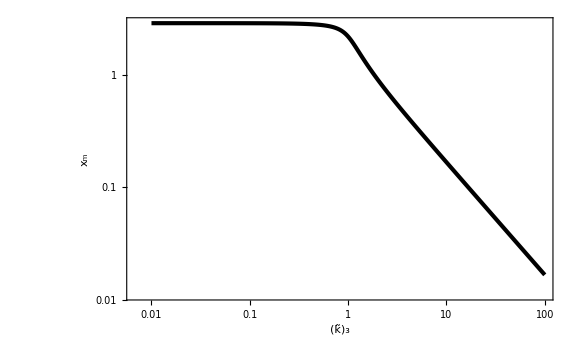

```mathematica
ListLogLogPlot[xmList,PlotRange->Full,FrameLabel->{Subscript[OverTilde[k], 3],Subscript[x, "m"]},PlotStyle->{Black,AbsoluteThickness[3]}]
```

```mathematica
xmint[k3t_]=Interpolation[xmList][k3t];
```

```mathematica
nu2inCk[Cm_,k3t_]=(Sqrt[1-3/2 Cm]-1)/(xmint[k3t] σ1^2/σ2 Sqrt[As]ζp[xmint[k3t],k3t]);
dnu2dCm[Cm_,k3t_]=D[nu2inCk[Cm,k3t], Cm]//Simplify;
```

```mathematica
f[x_]=1/2 x(x^2-3)(Erf[1/2 Sqrt[5/2]x]+Erf[Sqrt[5/2]x])+Sqrt[2/(5π)]((8/5+31/4 x^2)Exp[-5/8 x^2]+(-8/5+1/2 x^2)Exp[-5/2 x^2]);
P13[ν_,ξ_]=1/(2π Sqrt[1-γn^2])Exp[-1/2(ν^2+(ξ-γn ν)^2/(1-γn^2))];
npkPT[nu2_,k3t_]=2/(6π)^(3/2)(σ4/σ3)^3 nu2 k3t f[nu2 k3t^2]P13[nu2,nu2 k3t^2];
```

```mathematica
nCpt[Cm_]:=NIntegrate[npkPT[nu2inCk[Cm,k3t],k3t]Abs[dnu2dCm[Cm,k3t]],{k3t,5/10,3/2}(*,WorkingPrecision->30,MaxRecursion->12*)]
```

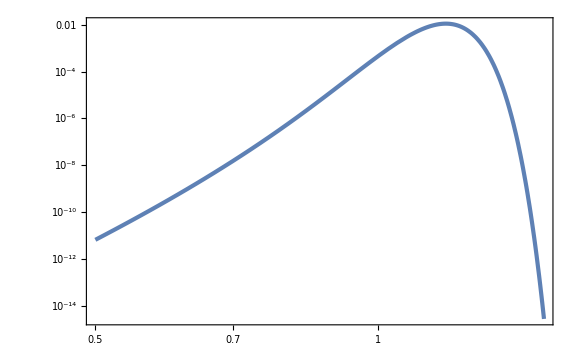

```mathematica
LogLogPlot[npkPT[nu2inCk[Cm,k3t],k3t]Abs[dnu2dCm[Cm,k3t]]/.{Cm->1/10},{k3t,5/10,3/2},WorkingPrecision->30]
```

```mathematica
nCptList=ParallelTable[{Cm,nCpt[Cm]},{Cm,10^-1,6/10,10^-2}];//AbsoluteTiming
```

{124.487,Null}

```mathematica
nCptint[Cm_]=Interpolation[nCptList][Cm];
```

### direct sampling

```mathematica
Nsim=10;
```

```mathematica
Lpeakdata=Table[Import["data/LN_Lpeak_0,05_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_"<>ToString[i]<>".csv"],{i,0,Nsim-1}];
```

```mathematica
HighLdata=Table[Select[Lpeakdata[[i]],#[[4]]>4σ2&],{i,Nsim}];
```

```mathematica
Cpeakdata=Table[Import["data/LN_Cpeak_0,05_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_"<>ToString[i]<>".csv"],{i,0,Nsim-1}];
```

```mathematica
HighCdata=Table[Select[Cpeakdata[[i]],#[[5]]>0.45&],{i,Nsim}];
```

```mathematica
matchQ[a_,b_]:=Max[Abs[a[[{1,2,3}]]-b[[{2,3,4}]]]]<=1;
```

```mathematica
onlyInC=Table[Select[HighCdata[[i]],Function[b,!AnyTrue[HighLdata[[i]],matchQ[#,b]&]]],{i,Nsim}];
```

```mathematica
γ3=σ3^2/(σ2 σ4);
f[x_]=1/2 x(x^2-3)(Erf[1/2 Sqrt[5/2]x]+Erf[Sqrt[5/2]x])+Sqrt[2/(5π)]((8/5+31/4 x^2)Exp[-5/8 x^2]+(-8/5+1/2 x^2)Exp[-5/2 x^2]);
P13[ν_,ξ_]=1/(2π Sqrt[1-γ3^2])Exp[-1/2(ν^2+(ξ-γ3 ν)^2/(1-γ3^2))];
npkPT[nu2_,k3t_]=2/(6π)^(3/2)σ4^3/σ3^3 nu2 k3t f[nu2 k3t^2]P13[nu2,nu2 k3t^2];
nnu2PT[nu2_]:=NIntegrate[npkPT[nu2,k3t],{k3t,0,∞}];
```

```mathematica
nudata=Flatten[Lpeakdata[[All,All,4]]/σ2];
nunBins=20;
nubinSpec={Min[nudata],Max[nudata],(Max[nudata]-Min[nudata])/nunBins};
```

```mathematica
nubinEdges=HistogramList[nudata,nubinSpec][[1]];
nubinCenters=MovingAverage[nubinEdges,2];
```

```mathematica
nuPDFPerList=HistogramList[(#[[All,4]])/σ2,nubinSpec,"PDF"][[2]]&/@Lpeakdata;
```

```mathematica
numeanPDF=Mean[nuPDFPerList];
nusePDF=StandardDeviation[nuPDFPerList]/Sqrt[Nsim];
```

```mathematica
nnu2Lat=Table[{nubinCenters[[i]],(numeanPDF[[i]]Length[nudata])/(Nsim NL^3)±(nusePDF[[i]]Length[nudata])/(Nsim NL^3)},{i,nunBins}];
```

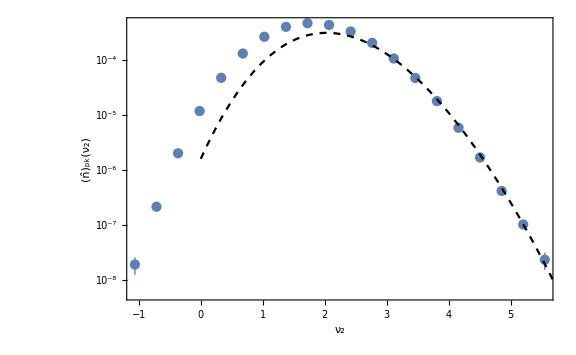

```mathematica
Show[ListLogPlot[nnu2Lat,Joined->False,FrameLabel->{{Subscript[OverHat[n], pk][Subscript[ν, 2]],None},{Subscript[ν, 2],σ^2==N[s2]}}(*,PlotRange->{10^-9,10^-3}*),PlotLegends->Placed[PointLegend[{"lattice"},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.6,0.2}]],LogPlot[nnu2PT[nu2],{nu2,0,6},PlotStyle->{Dashed,Black},PlotLegends->Placed[LineLegend[{"peak theory"},LegendMarkerSize->20,LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.6,0.2}]]]
```

```mathematica
Cdata=Flatten[Cpeakdata[[All,All,5]]];
CnBins=20;
CbinSpec={Min[Cdata],Max[Cdata],(Max[Cdata]-Min[Cdata])/CnBins};
```

```mathematica
CbinEdges=HistogramList[Cdata,CbinSpec][[1]];
CbinCenters=MovingAverage[CbinEdges,2];
```

```mathematica
CPDFPerList=HistogramList[#[[All,5]],CbinSpec,"PDF"][[2]]&/@Cpeakdata;
```

```mathematica
CmeanPDF=Mean[CPDFPerList];
CsePDF=StandardDeviation[CPDFPerList]/Sqrt[Nsim];
```

```mathematica
nCLat=Table[{CbinCenters[[i]],(CmeanPDF[[i]]Length[Cdata])/(Nsim NL^3)±(CsePDF[[i]]Length[Cdata])/(Nsim NL^3)},{i,CnBins}];
```

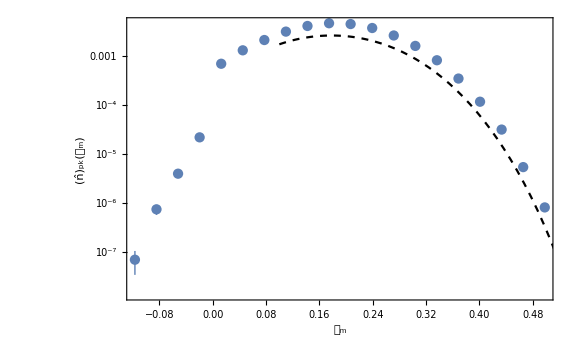

```mathematica
Show[ListLogPlot[nCLat,Joined->False,FrameLabel->{{Subscript[OverHat[n], pk][Subscript[𝒞, "m"]],None},{Subscript[𝒞, "m"],σ^2==N[s2]}},PlotLegends->Placed[PointLegend[{"lattice"},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.6,0.2}]],
LogPlot[nCptint[Cm],{Cm,0.1,0.6},PlotStyle->{Black,Dashed},PlotLegends->Placed[LineLegend[{"peak theory"},LegendMarkerSize->20,LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.6,0.2}]]]
```

## Lognormal σ^2=0.1

```mathematica
npeak=32;
NL=512;
As=10^-2;(*3.625 10^-3;*)
```

```mathematica
kpeak=2π npeak/NL
```

π/8

```mathematica
s2=10^-1;
```

```mathematica
σ1=Sqrt[E^(2 n^2 s2)kpeak^(2n)]/.{n->1};
σ2=Sqrt[E^(2 n^2 s2)kpeak^(2n)]/.{n->2};
σ3=Sqrt[E^(2 n^2 s2)kpeak^(2n)]/.{n->3};
σ4=Sqrt[E^(2 n^2 s2)kpeak^(2n)]/.{n->4};
```

### peak theory

```mathematica
calPz[lnk_]=1/Sqrt[2π s2] Exp[-lnk^2/(2s2)];
```

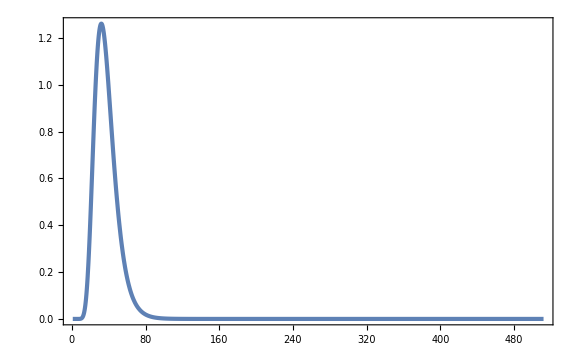

```mathematica
Plot[calPz[Log[n/npeak]],{n,1,NL},PlotRange->Full]
```

```mathematica
R3=Sqrt[3] σ3/σ4
```

(8 √3)/(ⅇ^(7/10) π)

```mathematica
R3//N
```

2.19025

```mathematica
γn=E^(-2s2)
```

1/ⅇ^(1/5)

```mathematica
ψ1[x_]:=kpeak^2/σ1^2 NIntegrate[E^(2lnk)calPz[lnk]Sinc[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
ψ2[x_]:=kpeak^4/σ2^2 NIntegrate[E^(4lnk)calPz[lnk]Sinc[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
ψ1p[x_]:=kpeak^2/σ1^2 NIntegrate[E^(3lnk)calPz[lnk]Sinc'[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
ψ2p[x_]:=kpeak^4/σ2^2 NIntegrate[E^(5lnk)calPz[lnk]Sinc'[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
ψ1pp[x_]:=kpeak^2/σ1^2 NIntegrate[E^(4lnk)calPz[lnk]Sinc''[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
ψ2pp[x_]:=kpeak^4/σ2^2 NIntegrate[E^(6lnk)calPz[lnk]Sinc''[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
```

```mathematica
AbsoluteTiming[
ψ1List=ParallelTable[{x,ψ1[x]},{x,10^-2,10,10^-2}];
ψ1pList=ParallelTable[{x,ψ1p[x]},{x,10^-2,10,10^-2}];
ψ1ppList=ParallelTable[{x,ψ1pp[x]},{x,10^-2,10,10^-2}];
ψ2List=ParallelTable[{x,ψ2[x]},{x,10^-2,10,10^-2}];
ψ2pList=ParallelTable[{x,ψ2p[x]},{x,10^-2,10,10^-2}];
ψ2ppList=ParallelTable[{x,ψ2pp[x]},{x,10^-2,10,10^-2}];]
```

{21.6894,Null}

```mathematica
ψ1int[x_]=Interpolation[ψ1List][x];
ψ1pint[x_]=Interpolation[ψ1pList][x];
ψ1ppint[x_]=Interpolation[ψ1ppList][x];
ψ2int[x_]=Interpolation[ψ2List][x];
ψ2pint[x_]=Interpolation[ψ2pList][x];
ψ2ppint[x_]=Interpolation[ψ2ppList][x];
```

```mathematica
ζx[x_,k3t_]=(1/(1-γn^2)(ψ1int[x]-1/3 R3^2 σ2^2/σ1^2 ψ2int[x])-k3t^2/(γn(1-γn^2))(γn^2 ψ1int[x]-1/3 R3^2 σ2^2/σ1^2 ψ2int[x]));
ζp[x_,k3t_]=(1/(1-γn^2)(ψ1pint[x]-1/3 R3^2 σ2^2/σ1^2 ψ2pint[x])-k3t^2/(γn(1-γn^2))(γn^2 ψ1pint[x]-1/3 R3^2 σ2^2/σ1^2 ψ2pint[x]));
ζpp[x_,k3t_]=(1/(1-γn^2)(ψ1ppint[x]-1/3 R3^2 σ2^2/σ1^2 ψ2ppint[x])-k3t^2/(γn(1-γn^2))(γn^2 ψ1ppint[x]-1/3 R3^2 σ2^2/σ1^2 ψ2ppint[x]));
```

```mathematica
CmCond[x_,k3t_]=(ζp[x,k3t]+x ζpp[x,k3t])/x^3;
```

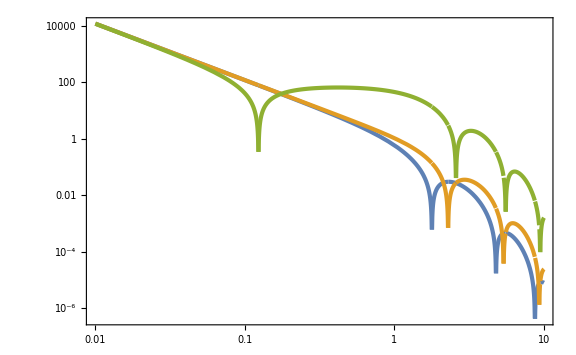

```mathematica
LogLogPlot[{Abs[CmCond[x,1]],Abs[CmCond[x,10^-2]],Abs[CmCond[x,10]]},{x,10^-2,10}]
```

```mathematica
xmList=ParallelTable[{10^lnk3t,x/.FindRoot[CmCond[x,10^lnk3t]==0,{x,Min[1/(2 10^lnk3t),1]},WorkingPrecision->30]//Quiet},{lnk3t,-2,2,10^-2}];
```

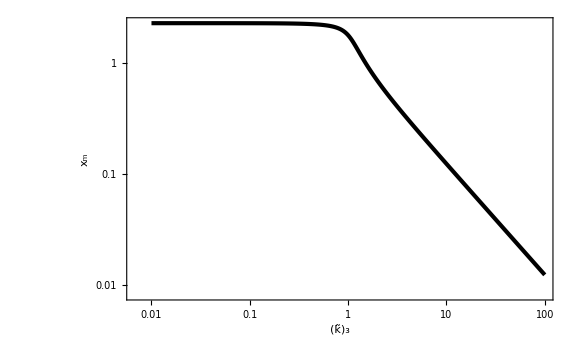

```mathematica
ListLogLogPlot[xmList,PlotRange->Full,FrameLabel->{Subscript[OverTilde[k], 3],Subscript[x, "m"]},PlotStyle->{Black,AbsoluteThickness[3]}]
```

```mathematica
xmint[k3t_]=Interpolation[xmList][k3t];
```

```mathematica
nu2inCk[Cm_,k3t_]=(Sqrt[1-3/2 Cm]-1)/(xmint[k3t] σ1^2/σ2 Sqrt[As]ζp[xmint[k3t],k3t]);
dnu2dCm[Cm_,k3t_]=D[nu2inCk[Cm,k3t], Cm]//Simplify;
```

```mathematica
f[x_]=1/2 x(x^2-3)(Erf[1/2 Sqrt[5/2]x]+Erf[Sqrt[5/2]x])+Sqrt[2/(5π)]((8/5+31/4 x^2)Exp[-5/8 x^2]+(-8/5+1/2 x^2)Exp[-5/2 x^2]);
P13[ν_,ξ_]=1/(2π Sqrt[1-γn^2])Exp[-1/2(ν^2+(ξ-γn ν)^2/(1-γn^2))];
npkPT[nu2_,k3t_]=2/(6π)^(3/2)(σ4/σ3)^3 nu2 k3t f[nu2 k3t^2]P13[nu2,nu2 k3t^2];
```

```mathematica
nCpt[Cm_]:=NIntegrate[npkPT[nu2inCk[Cm,k3t],k3t]Abs[dnu2dCm[Cm,k3t]],{k3t,5/10,3/2}(*,WorkingPrecision->30,MaxRecursion->12*)]
```

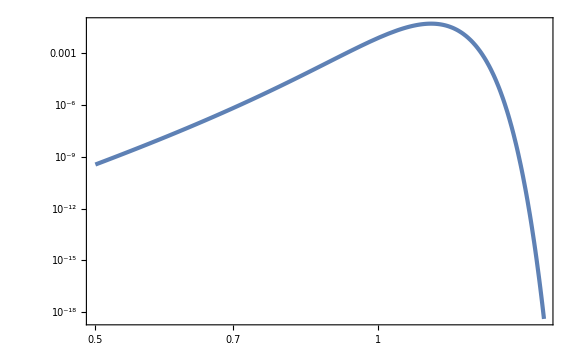

```mathematica
LogLogPlot[npkPT[nu2inCk[Cm,k3t],k3t]Abs[dnu2dCm[Cm,k3t]]/.{Cm->1/10},{k3t,5/10,3/2},WorkingPrecision->30]
```

```mathematica
nCptList=ParallelTable[{Cm,nCpt[Cm]},{Cm,10^-1,6/10,10^-2}];//AbsoluteTiming
```

{115.571,Null}

```mathematica
nCptint[Cm_]=Interpolation[nCptList][Cm];
```

### direct sampling

```mathematica
Nsim=10;
```

```mathematica
Lpeakdata=Table[Import["data/As=1e-2/LN_Lpeak_0,1_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_"<>ToString[i]<>".csv"],{i,0,Nsim-1}];
```

```mathematica
HighLdata=Table[Select[Lpeakdata[[i]],#[[4]]>4σ2&],{i,Nsim}];
```

```mathematica
Cpeakdata=Table[Import["data/As=1e-2/LN_Cpeak_0,1_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_"<>ToString[i]<>".csv"],{i,0,Nsim-1}];
```

```mathematica
HighCdata=Table[Select[Cpeakdata[[i]],#[[5]]>0.45&],{i,Nsim}];
```

```mathematica
matchQ[a_,b_]:=Max[Abs[a[[{1,2,3}]]-b[[{2,3,4}]]]]<=1;
```

```mathematica
onlyInC=Table[Select[HighCdata[[i]],Function[b,!AnyTrue[HighLdata[[i]],matchQ[#,b]&]]],{i,Nsim}];
```

```mathematica
Length[HighCdata]
Length[onlyInC]
```

10

10

```mathematica
γ3=σ3^2/(σ2 σ4);
f[x_]=1/2 x(x^2-3)(Erf[1/2 Sqrt[5/2]x]+Erf[Sqrt[5/2]x])+Sqrt[2/(5π)]((8/5+31/4 x^2)Exp[-5/8 x^2]+(-8/5+1/2 x^2)Exp[-5/2 x^2]);
P13[ν_,ξ_]=1/(2π Sqrt[1-γ3^2])Exp[-1/2(ν^2+(ξ-γ3 ν)^2/(1-γ3^2))];
npkPT[nu2_,k3t_]=2/(6π)^(3/2)σ4^3/σ3^3 nu2 k3t f[nu2 k3t^2]P13[nu2,nu2 k3t^2];
nnu2PT[nu2_]:=NIntegrate[npkPT[nu2,k3t],{k3t,0,∞}];
```

```mathematica
nudata=Flatten[Lpeakdata[[All,All,4]]/σ2];
nunBins=20;
nubinSpec={Min[nudata],Max[nudata],(Max[nudata]-Min[nudata])/nunBins};
```

```mathematica
nubinEdges=HistogramList[nudata,nubinSpec][[1]];
nubinCenters=MovingAverage[nubinEdges,2];
```

```mathematica
nuPDFPerList=HistogramList[(#[[All,4]])/σ2,nubinSpec,"PDF"][[2]]&/@Lpeakdata;
```

```mathematica
numeanPDF=Mean[nuPDFPerList];
nusePDF=StandardDeviation[nuPDFPerList]/Sqrt[Nsim];
```

```mathematica
nnu2Lat=Table[{nubinCenters[[i]],(numeanPDF[[i]]Length[nudata])/(Nsim NL^3)±(nusePDF[[i]]Length[nudata])/(Nsim NL^3)},{i,nunBins}];
```

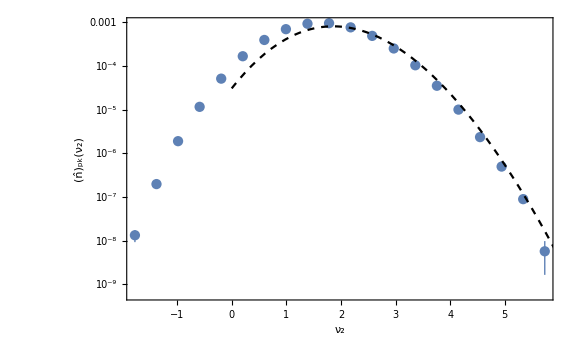

```mathematica
Show[ListLogPlot[nnu2Lat,Joined->False,FrameLabel->{{Subscript[OverHat[n], pk][Subscript[ν, 2]],None},{Subscript[ν, 2],σ^2==N[s2]}}(*,PlotRange->{10^-9,10^-3}*),PlotLegends->Placed[PointLegend[{"lattice"},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.6,0.2}]],LogPlot[nnu2PT[nu2],{nu2,0,6},PlotStyle->{Dashed,Black},PlotLegends->Placed[LineLegend[{"peak theory"},LegendMarkerSize->20,LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.6,0.2}]]]
```

```mathematica
Cdata=Flatten[Cpeakdata[[All,All,5]]];
CnBins=20;
CbinSpec={Min[Cdata],Max[Cdata],(Max[Cdata]-Min[Cdata])/CnBins};
```

```mathematica
CbinEdges=HistogramList[Cdata,CbinSpec][[1]];
CbinCenters=MovingAverage[CbinEdges,2];
```

```mathematica
CPDFPerList=HistogramList[#[[All,5]],CbinSpec,"PDF"][[2]]&/@Cpeakdata;
```

```mathematica
CmeanPDF=Mean[CPDFPerList];
CsePDF=StandardDeviation[CPDFPerList]/Sqrt[Nsim];
```

```mathematica
nCLat=Table[{CbinCenters[[i]],(CmeanPDF[[i]]Length[Cdata])/(Nsim NL^3)±(CsePDF[[i]]Length[Cdata])/(Nsim NL^3)},{i,CnBins}];
```

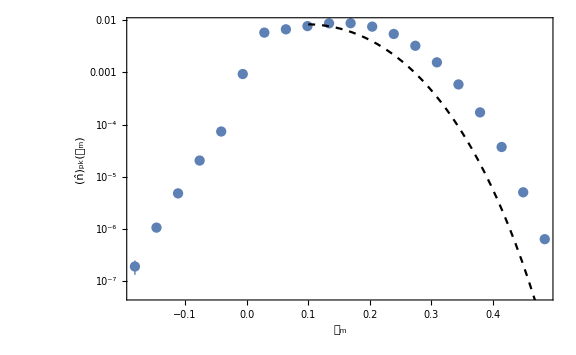

```mathematica
Show[ListLogPlot[nCLat,Joined->False,FrameLabel->{{Subscript[OverHat[n], pk][Subscript[𝒞, "m"]],None},{Subscript[𝒞, "m"],σ^2==N[s2]}},PlotLegends->Placed[PointLegend[{"lattice"},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.6,0.2}]],
LogPlot[nCptint[Cm],{Cm,0.1,0.6},PlotStyle->{Black,Dashed},PlotLegends->Placed[LineLegend[{"peak theory"},LegendMarkerSize->20,LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.6,0.2}]]]
```

## Lognormal σ^2=0.1 nsigma = 16

```mathematica
npeak=16;
NL=512;
As=10^-2;(*3.625 10^-3;*)
```

```mathematica
kpeak=2π npeak/NL
```

π/16

```mathematica
s2=10^-1;
```

```mathematica
σ1=Sqrt[E^(2 n^2 s2)kpeak^(2n)]/.{n->1};
σ2=Sqrt[E^(2 n^2 s2)kpeak^(2n)]/.{n->2};
σ3=Sqrt[E^(2 n^2 s2)kpeak^(2n)]/.{n->3};
σ4=Sqrt[E^(2 n^2 s2)kpeak^(2n)]/.{n->4};
```

### peak theory

```mathematica
calPz[lnk_]=1/Sqrt[2π s2] Exp[-lnk^2/(2s2)];
```

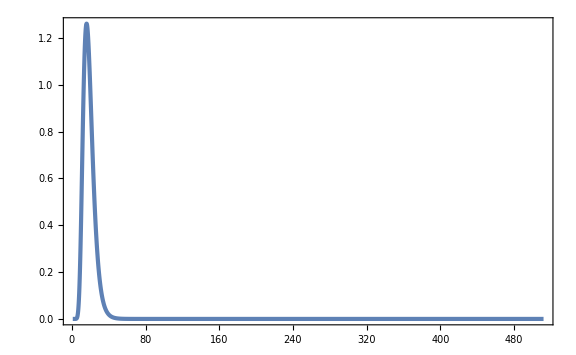

```mathematica
Plot[calPz[Log[n/npeak]],{n,1,NL},PlotRange->Full]
```

```mathematica
R3=Sqrt[3] σ3/σ4
```

(16 √3)/(ⅇ^(7/10) π)

```mathematica
R3//N
```

4.38051

```mathematica
γn=E^(-2s2)
```

1/ⅇ^(1/5)

```mathematica
ψ1[x_]:=kpeak^2/σ1^2 NIntegrate[E^(2lnk)calPz[lnk]Sinc[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
ψ2[x_]:=kpeak^4/σ2^2 NIntegrate[E^(4lnk)calPz[lnk]Sinc[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
ψ1p[x_]:=kpeak^2/σ1^2 NIntegrate[E^(3lnk)calPz[lnk]Sinc'[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
ψ2p[x_]:=kpeak^4/σ2^2 NIntegrate[E^(5lnk)calPz[lnk]Sinc'[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
ψ1pp[x_]:=kpeak^2/σ1^2 NIntegrate[E^(4lnk)calPz[lnk]Sinc''[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
ψ2pp[x_]:=kpeak^4/σ2^2 NIntegrate[E^(6lnk)calPz[lnk]Sinc''[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
```

```mathematica
AbsoluteTiming[
ψ1List=ParallelTable[{x,ψ1[x]},{x,10^-2,10,10^-2}];
ψ1pList=ParallelTable[{x,ψ1p[x]},{x,10^-2,10,10^-2}];
ψ1ppList=ParallelTable[{x,ψ1pp[x]},{x,10^-2,10,10^-2}];
ψ2List=ParallelTable[{x,ψ2[x]},{x,10^-2,10,10^-2}];
ψ2pList=ParallelTable[{x,ψ2p[x]},{x,10^-2,10,10^-2}];
ψ2ppList=ParallelTable[{x,ψ2pp[x]},{x,10^-2,10,10^-2}];]
```

{36.5718,Null}

```mathematica
ψ1int[x_]=Interpolation[ψ1List][x];
ψ1pint[x_]=Interpolation[ψ1pList][x];
ψ1ppint[x_]=Interpolation[ψ1ppList][x];
ψ2int[x_]=Interpolation[ψ2List][x];
ψ2pint[x_]=Interpolation[ψ2pList][x];
ψ2ppint[x_]=Interpolation[ψ2ppList][x];
```

```mathematica
ζx[x_,k3t_]=(1/(1-γn^2)(ψ1int[x]-1/3 R3^2 σ2^2/σ1^2 ψ2int[x])-k3t^2/(γn(1-γn^2))(γn^2 ψ1int[x]-1/3 R3^2 σ2^2/σ1^2 ψ2int[x]));
ζp[x_,k3t_]=(1/(1-γn^2)(ψ1pint[x]-1/3 R3^2 σ2^2/σ1^2 ψ2pint[x])-k3t^2/(γn(1-γn^2))(γn^2 ψ1pint[x]-1/3 R3^2 σ2^2/σ1^2 ψ2pint[x]));
ζpp[x_,k3t_]=(1/(1-γn^2)(ψ1ppint[x]-1/3 R3^2 σ2^2/σ1^2 ψ2ppint[x])-k3t^2/(γn(1-γn^2))(γn^2 ψ1ppint[x]-1/3 R3^2 σ2^2/σ1^2 ψ2ppint[x]));
```

```mathematica
CmCond[x_,k3t_]=(ζp[x,k3t]+x ζpp[x,k3t])/x^3;
```

```mathematica
LogLogPlot[{Abs[CmCond[x,1]],Abs[CmCond[x,10^-2]],Abs[CmCond[x,10]]},{x,10^-2,10}]
```

-Graphics-

```mathematica
xmList=ParallelTable[{10^lnk3t,x/.FindRoot[CmCond[x,10^lnk3t]==0,{x,Min[1/(2 10^lnk3t),1]},WorkingPrecision->30]//Quiet},{lnk3t,-2,2,10^-2}];
```

```mathematica
ListLogLogPlot[xmList,PlotRange->Full,FrameLabel->{Subscript[OverTilde[k], 3],Subscript[x, "m"]},PlotStyle->{Black,AbsoluteThickness[3]}]
```

-Graphics-

```mathematica
xmint[k3t_]=Interpolation[xmList][k3t];
```

```mathematica
nu2inCk[Cm_,k3t_]=(Sqrt[1-3/2 Cm]-1)/(xmint[k3t] σ1^2/σ2 Sqrt[As]ζp[xmint[k3t],k3t]);
dnu2dCm[Cm_,k3t_]=D[nu2inCk[Cm,k3t], Cm]//Simplify;
```

```mathematica
f[x_]=1/2 x(x^2-3)(Erf[1/2 Sqrt[5/2]x]+Erf[Sqrt[5/2]x])+Sqrt[2/(5π)]((8/5+31/4 x^2)Exp[-5/8 x^2]+(-8/5+1/2 x^2)Exp[-5/2 x^2]);
P13[ν_,ξ_]=1/(2π Sqrt[1-γn^2])Exp[-1/2(ν^2+(ξ-γn ν)^2/(1-γn^2))];
npkPT[nu2_,k3t_]=2/(6π)^(3/2)(σ4/σ3)^3 nu2 k3t f[nu2 k3t^2]P13[nu2,nu2 k3t^2];
```

```mathematica
nCpt[Cm_]:=NIntegrate[npkPT[nu2inCk[Cm,k3t],k3t]Abs[dnu2dCm[Cm,k3t]],{k3t,5/10,3/2}(*,WorkingPrecision->30,MaxRecursion->12*)]
```

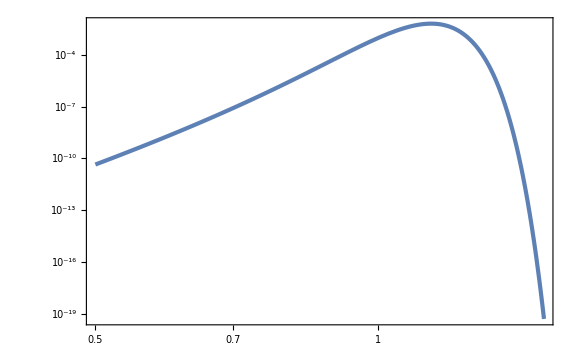

```mathematica
LogLogPlot[npkPT[nu2inCk[Cm,k3t],k3t]Abs[dnu2dCm[Cm,k3t]]/.{Cm->1/10},{k3t,5/10,3/2},WorkingPrecision->30]
```

```mathematica
nCptList=ParallelTable[{Cm,nCpt[Cm]},{Cm,10^-1,6/10,10^-2}];//AbsoluteTiming
```

{154.808,Null}

```mathematica
nCptint[Cm_]=Interpolation[nCptList][Cm];
```

### direct sampling

```mathematica
Nsim=10;
```

```mathematica
Lpeakdata=Table[Import["data/As=1e-2/LN_Lpeak_0,1_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_"<>ToString[i]<>".csv"],{i,0,Nsim-1}];
```

```mathematica
HighLdata=Table[Select[Lpeakdata[[i]],#[[4]]>4σ2&],{i,Nsim}];
```

```mathematica
Cpeakdata=Table[Import["data/As=1e-2/LN_Cpeak_0,1_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_"<>ToString[i]<>".csv"],{i,0,Nsim-1}];
```

```mathematica
HighCdata=Table[Select[Cpeakdata[[i]],#[[5]]>0.45&],{i,Nsim}];
```

```mathematica
matchQ[a_,b_]:=Max[Abs[a[[{1,2,3}]]-b[[{2,3,4}]]]]<=1;
```

```mathematica
onlyInC=Table[Select[HighCdata[[i]],Function[b,!AnyTrue[HighLdata[[i]],matchQ[#,b]&]]],{i,Nsim}];
```

```mathematica
Length[HighCdata[[1]]]
Length[onlyInC[[1]]]
```

4

4

```mathematica
HighCdata[[1]]
```

{{11,406,282,442,0.456962},{13,493,23,503,0.460635},{14,122,407,240,0.46125},{14,492,22,503,0.458341}}

```mathematica
HighLdata[[1]]
```

{{4,336,147,0.242516,0.300264},{8,309,139,0.231806,0.322038},{9,309,140,0.234852,0.33072},{10,485,96,0.236838,0.372789},{14,93,103,0.278948,0.340454},{17,46,344,0.259798,0.362669},{21,426,486,0.230418,0.355526},{23,138,422,0.261263,0.376711},{27,332,171,0.243916,0.350296},{32,330,217,0.246479,0.298791},{37,101,448,0.241195,0.331624},{39,258,365,0.230366,0.31622},{47,282,268,0.253704,0.33692},{52,26,454,0.247623,0.379416},{57,198,96,0.240084,0.27528},{57,230,246,0.261621,0.304721},{58,230,247,0.269224,0.313998},{59,229,248,0.272445,0.32905},{59,423,307,0.23171,0.375378},{62,289,105,0.243189,0.330533},{64,63,450,0.237504,0.355915},{65,176,188,0.239799,0.327399},{81,313,41,0.238367,0.337375},{81,438,368,0.237894,0.326386},{82,314,42,0.25246,0.331264},{93,148,405,0.279317,0.319047},{93,332,242,0.266787,0.31771},{99,405,58,0.233032,0.30196},{101,157,95,0.283293,0.338303},{106,472,257,0.235239,0.295607},{107,299,242,0.252414,0.312425},{110,420,17,0.2344,0.345006},{112,53,219,0.237162,0.355207},{120,2,452,0.254513,0.374305},{120,86,326,0.244752,0.334816},{124,326,340,0.245562,0.331833},{125,268,114,0.270048,0.372001},{126,269,114,0.273018,0.37713},{129,100,7,0.250501,0.348736},{129,331,506,0.233962,0.349688},{130,50,35,0.24071,0.318097},{131,423,366,0.239693,0.367334},{133,334,265,0.256721,0.36891},{142,150,329,0.23221,0.350035},{149,149,510,0.238195,0.309437},{157,277,384,0.269067,0.344904},{164,352,99,0.252524,0.348488},{167,441,231,0.232212,0.36269},{175,419,271,0.242337,0.320049},{177,287,473,0.245227,0.361158},{178,402,324,0.24763,0.36295},{186,104,131,0.234921,0.282111},{187,106,130,0.240612,0.301603},{188,107,129,0.242295,0.323809},{190,350,210,0.233473,0.387143},{194,329,40,0.248116,0.361988},{194,497,66,0.258227,0.310565},{201,94,236,0.237813,0.301597},{205,386,302,0.230164,0.316289},{209,2,457,0.246383,0.351933},{211,264,342,0.233043,0.356974},{213,117,187,0.251328,0.32125},{213,488,35,0.241611,0.337232},{220,85,207,0.240048,0.342428},{222,276,139,0.258982,0.347211},{226,499,289,0.239383,0.283945},{235,234,91,0.261063,0.350937},{237,46,190,0.258681,0.309781},{238,489,24,0.234957,0.332082},{239,490,23,0.236673,0.328007},{244,120,71,0.23318,0.35266},{252,244,135,0.235237,0.33169},{255,132,286,0.23554,0.3703},{263,262,166,0.24698,0.313918},{277,293,266,0.235075,0.283546},{279,191,432,0.284109,0.35927},{285,220,353,0.230994,0.364499},{294,22,159,0.253276,0.284382},{294,251,166,0.2576,0.350737},{304,466,501,0.25435,0.373787},{310,89,137,0.24116,0.310326},{317,409,315,0.233654,0.312193},{317,410,314,0.234999,0.33005},{318,300,340,0.232159,0.361714},{328,72,246,0.237769,0.324923},{336,177,352,0.244758,0.347304},{342,26,133,0.259047,0.31574},{345,504,268,0.247122,0.274489},{346,503,268,0.248149,0.274615},{347,213,376,0.244346,0.360006},{347,267,198,0.283249,0.377605},{347,502,268,0.247024,0.278367},{348,213,377,0.251325,0.362161},{357,166,276,0.258001,0.340544},{362,297,37,0.231004,0.350171},{366,5,109,0.253923,0.338484},{367,74,65,0.243183,0.295448},{383,185,340,0.265165,0.341884},{390,304,151,0.247384,0.347271},{391,227,350,0.230277,0.330335},{393,232,444,0.234823,0.348934},{395,83,258,0.230622,0.33535},{396,411,448,0.253058,0.370751},{396,412,447,0.255074,0.374522},{403,284,445,0.230969,0.2548},{404,348,17,0.233786,0.34325},{407,377,494,0.234871,0.319208},{418,272,89,0.234958,0.358295},{418,395,134,0.237198,0.326891},{419,250,359,0.23414,0.327829},{420,290,75,0.231334,0.351186},{424,447,59,0.297211,0.311487},{429,222,291,0.263595,0.334161},{431,91,245,0.243815,0.32671},{434,356,299,0.232681,0.327514},{437,345,329,0.240622,0.348931},{450,495,117,0.230062,0.352737},{453,217,178,0.230984,0.35127},{453,343,226,0.237993,0.339535},{456,115,7,0.272579,0.338104},{456,455,260,0.296339,0.311073},{458,371,360,0.244702,0.325806},{472,32,54,0.237541,0.343056},{478,336,478,0.259095,0.343858},{478,337,477,0.258122,0.356167},{486,405,108,0.249458,0.321704},{487,275,18,0.289337,0.3088},{490,6,57,0.241974,0.351839},{491,32,82,0.237956,0.306423},{495,136,370,0.232349,0.339817},{495,328,125,0.246022,0.332889},{500,341,185,0.230984,0.350089},{503,32,348,0.254018,0.358238},{506,327,503,0.232505,0.39799}}

```mathematica
γ3=σ3^2/(σ2 σ4);
f[x_]=1/2 x(x^2-3)(Erf[1/2 Sqrt[5/2]x]+Erf[Sqrt[5/2]x])+Sqrt[2/(5π)]((8/5+31/4 x^2)Exp[-5/8 x^2]+(-8/5+1/2 x^2)Exp[-5/2 x^2]);
P13[ν_,ξ_]=1/(2π Sqrt[1-γ3^2])Exp[-1/2(ν^2+(ξ-γ3 ν)^2/(1-γ3^2))];
npkPT[nu2_,k3t_]=2/(6π)^(3/2)σ4^3/σ3^3 nu2 k3t f[nu2 k3t^2]P13[nu2,nu2 k3t^2];
nnu2PT[nu2_]:=NIntegrate[npkPT[nu2,k3t],{k3t,0,∞}];
```

```mathematica
nudata=Flatten[Lpeakdata[[All,All,4]]/σ2];
nunBins=20;
nubinSpec={Min[nudata],Max[nudata],(Max[nudata]-Min[nudata])/nunBins};
```

```mathematica
nubinEdges=HistogramList[nudata,nubinSpec][[1]];
nubinCenters=MovingAverage[nubinEdges,2];
```

```mathematica
nuPDFPerList=HistogramList[(#[[All,4]])/σ2,nubinSpec,"PDF"][[2]]&/@Lpeakdata;
```

```mathematica
numeanPDF=Mean[nuPDFPerList];
nusePDF=StandardDeviation[nuPDFPerList]/Sqrt[Nsim];
```

```mathematica
nnu2Lat=Table[{nubinCenters[[i]],(numeanPDF[[i]]Length[nudata])/(Nsim NL^3)±(nusePDF[[i]]Length[nudata])/(Nsim NL^3)},{i,nunBins}];
```

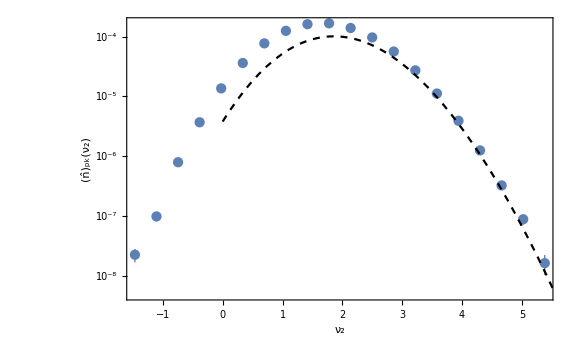

```mathematica
Show[ListLogPlot[nnu2Lat,Joined->False,FrameLabel->{{Subscript[OverHat[n], pk][Subscript[ν, 2]],None},{Subscript[ν, 2],σ^2==N[s2]}}(*,PlotRange->{10^-9,10^-3}*),PlotLegends->Placed[PointLegend[{"lattice"},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.6,0.2}]],LogPlot[nnu2PT[nu2],{nu2,0,6},PlotStyle->{Dashed,Black},PlotLegends->Placed[LineLegend[{"peak theory"},LegendMarkerSize->20,LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.6,0.2}]]]
```

```mathematica
Cdata=Flatten[Cpeakdata[[All,All,5]]];
CnBins=20;
CbinSpec={Min[Cdata],Max[Cdata],(Max[Cdata]-Min[Cdata])/CnBins};
```

```mathematica
CbinEdges=HistogramList[Cdata,CbinSpec][[1]];
CbinCenters=MovingAverage[CbinEdges,2];
```

```mathematica
CPDFPerList=HistogramList[#[[All,5]],CbinSpec,"PDF"][[2]]&/@Cpeakdata;
```

```mathematica
CmeanPDF=Mean[CPDFPerList];
CsePDF=StandardDeviation[CPDFPerList]/Sqrt[Nsim];
```

```mathematica
nCLat=Table[{CbinCenters[[i]],(CmeanPDF[[i]]Length[Cdata])/(Nsim NL^3)±(CsePDF[[i]]Length[Cdata])/(Nsim NL^3)},{i,CnBins}];
```

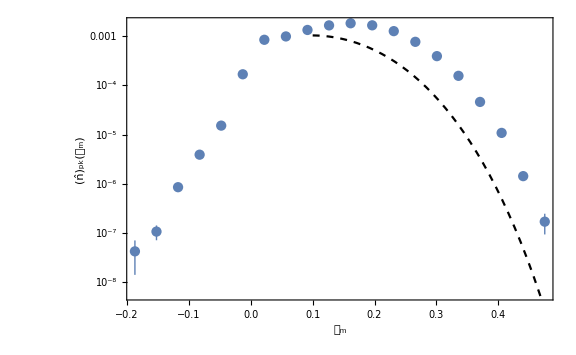

```mathematica
Show[ListLogPlot[nCLat,Joined->False,FrameLabel->{{Subscript[OverHat[n], pk][Subscript[𝒞, "m"]],None},{Subscript[𝒞, "m"],σ^2==N[s2]}},PlotLegends->Placed[PointLegend[{"lattice"},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.6,0.2}]],
LogPlot[nCptint[Cm],{Cm,0.1,0.6},PlotStyle->{Black,Dashed},PlotLegends->Placed[LineLegend[{"peak theory"},LegendMarkerSize->20,LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.6,0.2}]]]
```

## Lognormal σ^2=0.1 kUV

```mathematica
npeak=32;
NL=512;
As=10^-2;(*3.625 10^-3;*)
```

```mathematica
kpeak=2π npeak/NL
```

π/8

```mathematica
s2=10^-1;
kUV=kpeak;
```

### peak theory

```mathematica
calPz[lnk_]=1/Sqrt[2π s2] Exp[-lnk^2/(2s2)];
```

```mathematica
Plot[calPz[Log[n/npeak]],{n,1,NL},PlotRange->Full]
```

-Graphics-

```mathematica
σ1=kpeak Sqrt[NIntegrate[E^(2 lnk)1/Sqrt[2π s2] E^(-lnk^2/(2 s2)),{lnk,-∞,Log[kUV/kpeak]},Method->"GaussKronrodRule",WorkingPrecision->30]//Quiet]
σ2=kpeak^2 Sqrt[NIntegrate[E^(4 lnk)1/Sqrt[2π s2] E^(-lnk^2/(2 s2)),{lnk,-∞,Log[kUV/kpeak]},Method->"GaussKronrodRule",WorkingPrecision->30]//Quiet]
σ3=kpeak^3 Sqrt[NIntegrate[E^(6 lnk)1/Sqrt[2π s2] E^(-lnk^2/(2 s2)),{lnk,-∞,Log[kUV/kpeak]},Method->"GaussKronrodRule",WorkingPrecision->30]//Quiet]
σ4=kpeak^4 Sqrt[NIntegrate[E^(8 lnk)1/Sqrt[2π s2] E^(-lnk^2/(2 s2)),{lnk,-∞,Log[kUV/kpeak]},Method->"GaussKronrodRule",WorkingPrecision->30]//Quiet]
```

0.222800631942082783565101287647

0.0738166149676377021864625137131

0.0253172686424782591194027019504

0.00889769039393971235161572492911

```mathematica
R3=Sqrt[3] σ3/σ4
```

4.92833461900515305311347179308

```mathematica
γ3=σ3^2/(σ2 σ4)
```

0.97589318298925713706433459839

```mathematica
ψ1[x_]:=kpeak^2/σ1^2 NIntegrate[E^(2lnk)calPz[lnk]Sinc[E^lnk x],{lnk,-∞,Log[kUV/kpeak]},Method->"GaussKronrodRule",WorkingPrecision->30]
ψ2[x_]:=kpeak^4/σ2^2 NIntegrate[E^(4lnk)calPz[lnk]Sinc[E^lnk x],{lnk,-∞,Log[kUV/kpeak]},Method->"GaussKronrodRule",WorkingPrecision->30]
ψ1p[x_]:=kpeak^2/σ1^2 NIntegrate[E^(3lnk)calPz[lnk]Sinc'[E^lnk x],{lnk,-∞,Log[kUV/kpeak]},Method->"GaussKronrodRule",WorkingPrecision->30]
ψ2p[x_]:=kpeak^4/σ2^2 NIntegrate[E^(5lnk)calPz[lnk]Sinc'[E^lnk x],{lnk,-∞,Log[kUV/kpeak]},Method->"GaussKronrodRule",WorkingPrecision->30]
ψ1pp[x_]:=kpeak^2/σ1^2 NIntegrate[E^(4lnk)calPz[lnk]Sinc''[E^lnk x],{lnk,-∞,Log[kUV/kpeak]},Method->"GaussKronrodRule",WorkingPrecision->30]
ψ2pp[x_]:=kpeak^4/σ2^2 NIntegrate[E^(6lnk)calPz[lnk]Sinc''[E^lnk x],{lnk,-∞,Log[kUV/kpeak]},Method->"GaussKronrodRule",WorkingPrecision->30]
```

```mathematica
AbsoluteTiming[
ψ1List=ParallelTable[{x,ψ1[x]},{x,10^-2,10,10^-2}];
ψ1pList=ParallelTable[{x,ψ1p[x]},{x,10^-2,10,10^-2}];
ψ1ppList=ParallelTable[{x,ψ1pp[x]},{x,10^-2,10,10^-2}];
ψ2List=ParallelTable[{x,ψ2[x]},{x,10^-2,10,10^-2}];
ψ2pList=ParallelTable[{x,ψ2p[x]},{x,10^-2,10,10^-2}];
ψ2ppList=ParallelTable[{x,ψ2pp[x]},{x,10^-2,10,10^-2}];]
```

{6.53063,Null}

```mathematica
ψ1int[x_]=Interpolation[ψ1List][x];
ψ1pint[x_]=Interpolation[ψ1pList][x];
ψ1ppint[x_]=Interpolation[ψ1ppList][x];
ψ2int[x_]=Interpolation[ψ2List][x];
ψ2pint[x_]=Interpolation[ψ2pList][x];
ψ2ppint[x_]=Interpolation[ψ2ppList][x];
```

```mathematica
ζx[x_,k3t_]=(1/(1-γ3^2)(ψ1int[x]-1/3 R3^2 σ2^2/σ1^2 ψ2int[x])-k3t^2/(γ3(1-γ3^2))(γ3^2 ψ1int[x]-1/3 R3^2 σ2^2/σ1^2 ψ2int[x]));
ζp[x_,k3t_]=(1/(1-γ3^2)(ψ1pint[x]-1/3 R3^2 σ2^2/σ1^2 ψ2pint[x])-k3t^2/(γ3(1-γ3^2))(γ3^2 ψ1pint[x]-1/3 R3^2 σ2^2/σ1^2 ψ2pint[x]));
ζpp[x_,k3t_]=(1/(1-γ3^2)(ψ1ppint[x]-1/3 R3^2 σ2^2/σ1^2 ψ2ppint[x])-k3t^2/(γ3(1-γ3^2))(γ3^2 ψ1ppint[x]-1/3 R3^2 σ2^2/σ1^2 ψ2ppint[x]));
```

```mathematica
CmCond[x_,k3t_]=(ζp[x,k3t]+x ζpp[x,k3t])/x^3;
```

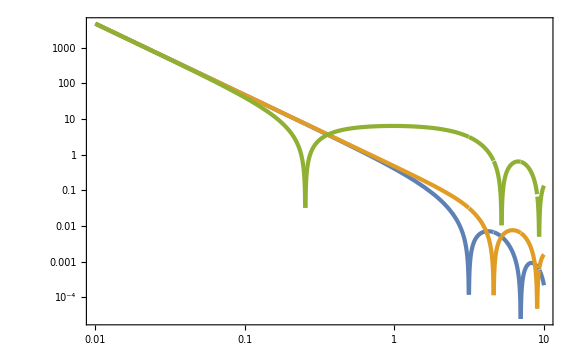

```mathematica
LogLogPlot[{Abs[CmCond[x,1]],Abs[CmCond[x,10^-2]],Abs[CmCond[x,10]]},{x,10^-2,10}]
```

```mathematica
xmList=ParallelTable[{10^lnk3t,x/.FindRoot[CmCond[x,10^lnk3t]==0,{x,Min[1/(2 10^lnk3t),1]},WorkingPrecision->30]//Quiet},{lnk3t,-2,2,10^-2}];
```

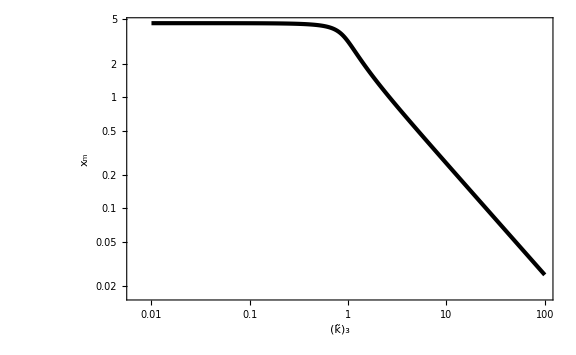

```mathematica
ListLogLogPlot[xmList,PlotRange->Full,FrameLabel->{Subscript[OverTilde[k], 3],Subscript[x, "m"]},PlotStyle->{Black,AbsoluteThickness[3]}]
```

```mathematica
xmint[k3t_]=Interpolation[xmList][k3t];
```

```mathematica
nu2inCk[Cm_,k3t_]=(Sqrt[1-3/2 Cm]-1)/(xmint[k3t] σ1^2/σ2 Sqrt[As]ζp[xmint[k3t],k3t]);
dnu2dCm[Cm_,k3t_]=D[nu2inCk[Cm,k3t], Cm]//Simplify;
```

```mathematica
f[x_]=1/2 x(x^2-3)(Erf[1/2 Sqrt[5/2]x]+Erf[Sqrt[5/2]x])+Sqrt[2/(5π)]((8/5+31/4 x^2)Exp[-5/8 x^2]+(-8/5+1/2 x^2)Exp[-5/2 x^2]);
P13[ν_,ξ_]=1/(2π Sqrt[1-γ3^2])Exp[-1/2(ν^2+(ξ-γ3 ν)^2/(1-γ3^2))];
npkPT[nu2_,k3t_]=2/(6π)^(3/2)(σ4/σ3)^3 nu2 k3t f[nu2 k3t^2]P13[nu2,nu2 k3t^2];
```

```mathematica
nCpt[Cm_]:=NIntegrate[npkPT[nu2inCk[Cm,k3t],k3t]Abs[dnu2dCm[Cm,k3t]],{k3t,5/10,3/2}(*,WorkingPrecision->30,MaxRecursion->12*)]
```

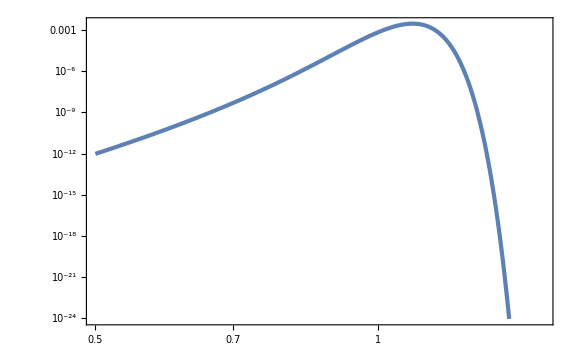

```mathematica
LogLogPlot[npkPT[nu2inCk[Cm,k3t],k3t]Abs[dnu2dCm[Cm,k3t]]/.{Cm->1/10},{k3t,5/10,3/2},WorkingPrecision->30]
```

```mathematica
nCptList=ParallelTable[{Cm,nCpt[Cm]},{Cm,10^-1,6/10,10^-2}];//AbsoluteTiming
```

{44.7811,Null}

```mathematica
nCptint[Cm_]=Interpolation[nCptList][Cm];
```

### direct sampling

```mathematica
Nsim=10;
```

```mathematica
Lpeakdata=Table[Import["data/As=1e-2/LN_Lpeak_0,1_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_"<>ToString[i]<>".csv"],{i,0,Nsim-1}];
```

```mathematica
HighLdata=Table[Select[Lpeakdata[[i]],#[[4]]>4σ2&],{i,Nsim}];
```

```mathematica
Cpeakdata=Table[Import["data/As=1e-2/LN_Cpeak_0,1_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_"<>ToString[i]<>".csv"],{i,0,Nsim-1}];
```

```mathematica
HighCdata=Table[Select[Cpeakdata[[i]],#[[5]]>0.45&],{i,Nsim}];
```

```mathematica
matchQ[a_,b_]:=Max[Abs[a[[{1,2,3}]]-b[[{2,3,4}]]]]<=1;
```

```mathematica
onlyInC=Table[Select[HighCdata[[i]],Function[b,!AnyTrue[HighLdata[[i]],matchQ[#,b]&]]],{i,Nsim}];
```

```mathematica
Length[HighCdata]
Length[onlyInC]
```

10

10

```mathematica
γ3=σ3^2/(σ2 σ4);
f[x_]=1/2 x(x^2-3)(Erf[1/2 Sqrt[5/2]x]+Erf[Sqrt[5/2]x])+Sqrt[2/(5π)]((8/5+31/4 x^2)Exp[-5/8 x^2]+(-8/5+1/2 x^2)Exp[-5/2 x^2]);
P13[ν_,ξ_]=1/(2π Sqrt[1-γ3^2])Exp[-1/2(ν^2+(ξ-γ3 ν)^2/(1-γ3^2))];
npkPT[nu2_,k3t_]=2/(6π)^(3/2)σ4^3/σ3^3 nu2 k3t f[nu2 k3t^2]P13[nu2,nu2 k3t^2];
nnu2PT[nu2_]:=NIntegrate[npkPT[nu2,k3t],{k3t,0,∞}];
```

```mathematica
nudata=Flatten[Lpeakdata[[All,All,4]]/σ2];
nunBins=20;
nubinSpec={Min[nudata],Max[nudata],(Max[nudata]-Min[nudata])/nunBins};
```

```mathematica
nubinEdges=HistogramList[nudata,nubinSpec][[1]];
nubinCenters=MovingAverage[nubinEdges,2];
```

```mathematica
nuPDFPerList=HistogramList[(#[[All,4]])/σ2,nubinSpec,"PDF"][[2]]&/@Lpeakdata;
```

```mathematica
numeanPDF=Mean[nuPDFPerList];
nusePDF=StandardDeviation[nuPDFPerList]/Sqrt[Nsim];
```

```mathematica
nnu2Lat=Table[{nubinCenters[[i]],(numeanPDF[[i]]Length[nudata])/(Nsim NL^3)±(nusePDF[[i]]Length[nudata])/(Nsim NL^3)},{i,nunBins}];
```

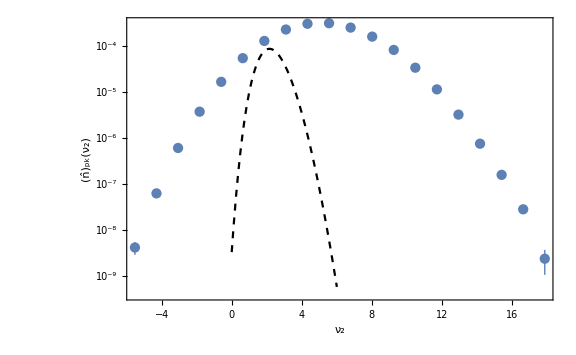

```mathematica
Show[ListLogPlot[nnu2Lat,Joined->False,FrameLabel->{{Subscript[OverHat[n], pk][Subscript[ν, 2]],None},{Subscript[ν, 2],σ^2==N[s2]}}(*,PlotRange->{10^-9,10^-3}*),PlotLegends->Placed[PointLegend[{"lattice"},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.6,0.2}]],LogPlot[nnu2PT[nu2],{nu2,0,6},PlotStyle->{Dashed,Black},PlotLegends->Placed[LineLegend[{"peak theory"},LegendMarkerSize->20,LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.6,0.2}]]]
```

```mathematica
Cdata=Flatten[Cpeakdata[[All,All,5]]];
CnBins=20;
CbinSpec={Min[Cdata],Max[Cdata],(Max[Cdata]-Min[Cdata])/CnBins};
```

```mathematica
CbinEdges=HistogramList[Cdata,CbinSpec][[1]];
CbinCenters=MovingAverage[CbinEdges,2];
```

```mathematica
CPDFPerList=HistogramList[#[[All,5]],CbinSpec,"PDF"][[2]]&/@Cpeakdata;
```

```mathematica
CmeanPDF=Mean[CPDFPerList];
CsePDF=StandardDeviation[CPDFPerList]/Sqrt[Nsim];
```

```mathematica
nCLat=Table[{CbinCenters[[i]],(CmeanPDF[[i]]Length[Cdata])/(Nsim NL^3)±(CsePDF[[i]]Length[Cdata])/(Nsim NL^3)},{i,CnBins}];
```

```mathematica
Show[ListLogPlot[nCLat,Joined->False,FrameLabel->{{Subscript[OverHat[n], pk][Subscript[𝒞, "m"]],None},{Subscript[𝒞, "m"],σ^2==N[s2]}},PlotLegends->Placed[PointLegend[{"lattice"},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.6,0.2}]],
LogPlot[nCptint[Cm],{Cm,0.1,0.6},PlotStyle->{Black,Dashed},PlotLegends->Placed[LineLegend[{"peak theory"},LegendMarkerSize->20,LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.6,0.2}]]]
```

-Graphics-

## Lognormal σ^2=0.2

```mathematica
npeak=32;
NL=512;
As=10^-2;(*3.625 10^-3;*)
```

```mathematica
kpeak=2π npeak/NL
```

π/8

```mathematica
s2=2 10^-1;
```

```mathematica
σ1=Sqrt[E^(2 n^2 s2)kpeak^(2n)]/.{n->1};
σ2=Sqrt[E^(2 n^2 s2)kpeak^(2n)]/.{n->2};
σ3=Sqrt[E^(2 n^2 s2)kpeak^(2n)]/.{n->3};
σ4=Sqrt[E^(2 n^2 s2)kpeak^(2n)]/.{n->4};
```

### peak theory

```mathematica
calPz[lnk_]=1/Sqrt[2π s2] Exp[-lnk^2/(2s2)];
```

```mathematica
R3=Sqrt[3] σ3/σ4
```

(8 √3)/(ⅇ^(7/5) π)

```mathematica
γn=E^(-2s2)
```

1/ⅇ^(2/5)

```mathematica
ψ1[x_]:=kpeak^2/σ1^2 NIntegrate[E^(2lnk)calPz[lnk]Sinc[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
ψ2[x_]:=kpeak^4/σ2^2 NIntegrate[E^(4lnk)calPz[lnk]Sinc[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
ψ1p[x_]:=kpeak^2/σ1^2 NIntegrate[E^(3lnk)calPz[lnk]Sinc'[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
ψ2p[x_]:=kpeak^4/σ2^2 NIntegrate[E^(5lnk)calPz[lnk]Sinc'[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
ψ1pp[x_]:=kpeak^2/σ1^2 NIntegrate[E^(4lnk)calPz[lnk]Sinc''[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
ψ2pp[x_]:=kpeak^4/σ2^2 NIntegrate[E^(6lnk)calPz[lnk]Sinc''[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
```

```mathematica
AbsoluteTiming[
ψ1List=ParallelTable[{x,ψ1[x]//Quiet},{x,10^-2,10,10^-2}];
ψ1pList=ParallelTable[{x,ψ1p[x]//Quiet},{x,10^-2,10,10^-2}];
ψ1ppList=ParallelTable[{x,ψ1pp[x]//Quiet},{x,10^-2,10,10^-2}];
ψ2List=ParallelTable[{x,ψ2[x]//Quiet},{x,10^-2,10,10^-2}];
ψ2pList=ParallelTable[{x,ψ2p[x]//Quiet},{x,10^-2,10,10^-2}];
ψ2ppList=ParallelTable[{x,ψ2pp[x]//Quiet},{x,10^-2,10,10^-2}];]
```

{29.8748,Null}

```mathematica
ψ1int[x_]=Interpolation[ψ1List][x];
ψ1pint[x_]=Interpolation[ψ1pList][x];
ψ1ppint[x_]=Interpolation[ψ1ppList][x];
ψ2int[x_]=Interpolation[ψ2List][x];
ψ2pint[x_]=Interpolation[ψ2pList][x];
ψ2ppint[x_]=Interpolation[ψ2ppList][x];
```

```mathematica
ζx[x_,k3t_]=(1/(1-γn^2)(ψ1int[x]-1/3 R3^2 σ2^2/σ1^2 ψ2int[x])-k3t^2/(γn(1-γn^2))(γn^2 ψ1int[x]-1/3 R3^2 σ2^2/σ1^2 ψ2int[x]));
ζp[x_,k3t_]=(1/(1-γn^2)(ψ1pint[x]-1/3 R3^2 σ2^2/σ1^2 ψ2pint[x])-k3t^2/(γn(1-γn^2))(γn^2 ψ1pint[x]-1/3 R3^2 σ2^2/σ1^2 ψ2pint[x]));
ζpp[x_,k3t_]=(1/(1-γn^2)(ψ1ppint[x]-1/3 R3^2 σ2^2/σ1^2 ψ2ppint[x])-k3t^2/(γn(1-γn^2))(γn^2 ψ1ppint[x]-1/3 R3^2 σ2^2/σ1^2 ψ2ppint[x]));
```

```mathematica
CmCond[x_,k3t_]=(ζp[x,k3t]+x ζpp[x,k3t])/x^3;
```

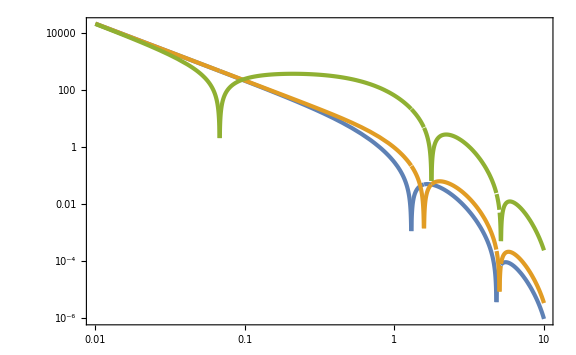

```mathematica
LogLogPlot[{Abs[CmCond[x,1]],Abs[CmCond[x,10^-2]],Abs[CmCond[x,10]]},{x,10^-2,10}]
```

```mathematica
xmList=ParallelTable[{10^lnk3t,x/.FindRoot[CmCond[x,10^lnk3t]==0,{x,Min[1/(2 10^lnk3t),0.05]},WorkingPrecision->30]//Quiet},{lnk3t,-2,2,10^-2}];
```

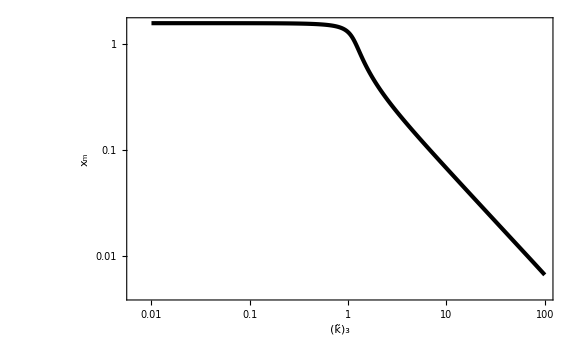

```mathematica
ListLogLogPlot[xmList,PlotRange->Full,FrameLabel->{Subscript[OverTilde[k], 3],Subscript[x, "m"]},PlotStyle->{Black,AbsoluteThickness[3]}]
```

```mathematica
xmint[k3t_]=Interpolation[xmList][k3t];
```

```mathematica
nu2inCk[Cm_,k3t_]=(Sqrt[1-3/2 Cm]-1)/(xmint[k3t] σ1^2/σ2 Sqrt[As]ζp[xmint[k3t],k3t]);
dnu2dCm[Cm_,k3t_]=D[nu2inCk[Cm,k3t], Cm]//Simplify;
```

```mathematica
f[x_]=1/2 x(x^2-3)(Erf[1/2 Sqrt[5/2]x]+Erf[Sqrt[5/2]x])+Sqrt[2/(5π)]((8/5+31/4 x^2)Exp[-5/8 x^2]+(-8/5+1/2 x^2)Exp[-5/2 x^2]);
P13[ν_,ξ_]=1/(2π Sqrt[1-γn^2])Exp[-1/2(ν^2+(ξ-γn ν)^2/(1-γn^2))];
npkPT[nu2_,k3t_]=2/(6π)^(3/2)(σ4/σ3)^3 nu2 k3t f[nu2 k3t^2]P13[nu2,nu2 k3t^2];
```

```mathematica
nCpt[Cm_]:=NIntegrate[npkPT[nu2inCk[Cm,k3t],k3t]Abs[dnu2dCm[Cm,k3t]],{k3t,1/10,3/2}(*,WorkingPrecision->30,MaxRecursion->12*)]
```

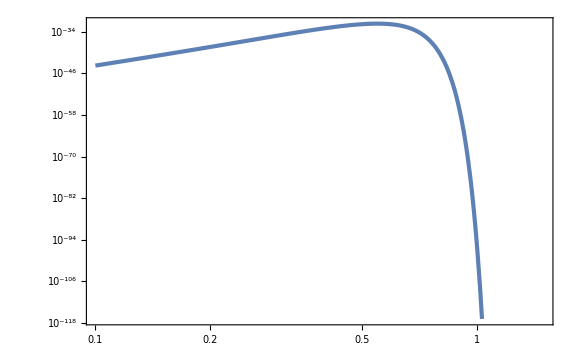

```mathematica
LogLogPlot[npkPT[nu2inCk[Cm,k3t],k3t]Abs[dnu2dCm[Cm,k3t]]/.{Cm->6/10},{k3t,1/10,3/2},WorkingPrecision->30]
```

```mathematica
nCpt[5/10]
```

3.24543×10^-18

```mathematica
nCptList=ParallelTable[{Cm,nCpt[Cm]},{Cm,10^-1,6/10,10^-2}];//AbsoluteTiming
```

{210.572,Null}

```mathematica
nCptint[Cm_]=Interpolation[nCptList][Cm];
```

### direct sampling

```mathematica
Nsim=10;
```

```mathematica
Lpeakdata=Table[Import["data/LN_Lpeak_0,2_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_"<>ToString[i]<>".csv"],{i,0,Nsim-1}];
```

```mathematica
HighLdata=Table[Select[Lpeakdata[[i]],#[[4]]>4σ2&],{i,Nsim}];
```

```mathematica
Cpeakdata=Table[Import["data/LN_Cpeak_0,2_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_"<>ToString[i]<>".csv"],{i,0,Nsim-1}];
```

```mathematica
HighCdata=Table[Select[Cpeakdata[[i]],#[[5]]>0.45&],{i,Nsim}];
```

```mathematica
HighCdata
```

{{{4,43,421,222,0.461824},{7,488,276,19,0.478991}},{{4,71,272,416,0.451021}},{{4,227,31,72,0.45599}},{{5,478,478,38,0.469243},{5,482,254,80,0.450418},{7,126,4,477,0.466538},{7,468,435,445,0.452097}},{{6,501,2,56,0.453136}},{{5,99,199,325,0.464088},{5,173,327,227,0.457168},{7,223,364,190,0.458006},{8,223,364,189,0.451987}},{{5,383,88,283,0.482896}},{{5,177,2,74,0.459678}},{{5,281,214,50,0.454028},{5,351,302,155,0.461731}},{{4,62,187,235,0.460302},{5,62,187,236,0.470164},{6,227,244,465,0.459463},{8,403,31,208,0.479828},{10,421,373,325,0.456722}}}

```mathematica
matchQ[a_,b_]:=Max[Abs[a[[{1,2,3}]]-b[[{2,3,4}]]]]<=1;
```

```mathematica
onlyInC=Table[Select[HighCdata[[i]],Function[b,!AnyTrue[HighLdata[[i]],matchQ[#,b]&]]],{i,Nsim}];
```

```mathematica
γ3=σ3^2/(σ2 σ4);
f[x_]=1/2 x(x^2-3)(Erf[1/2 Sqrt[5/2]x]+Erf[Sqrt[5/2]x])+Sqrt[2/(5π)]((8/5+31/4 x^2)Exp[-5/8 x^2]+(-8/5+1/2 x^2)Exp[-5/2 x^2]);
P13[ν_,ξ_]=1/(2π Sqrt[1-γ3^2])Exp[-1/2(ν^2+(ξ-γ3 ν)^2/(1-γ3^2))];
npkPT[nu2_,k3t_]=2/(6π)^(3/2)σ4^3/σ3^3 nu2 k3t f[nu2 k3t^2]P13[nu2,nu2 k3t^2];
nnu2PT[nu2_]:=NIntegrate[npkPT[nu2,k3t],{k3t,0,∞}];
```

```mathematica
nudata=Flatten[Lpeakdata[[All,All,4]]/σ2];
nunBins=20;
nubinSpec={Min[nudata],Max[nudata],(Max[nudata]-Min[nudata])/nunBins};
```

```mathematica
nubinEdges=HistogramList[nudata,nubinSpec][[1]];
nubinCenters=MovingAverage[nubinEdges,2];
```

```mathematica
nuPDFPerList=HistogramList[(#[[All,4]])/σ2,nubinSpec,"PDF"][[2]]&/@Lpeakdata;
```

```mathematica
numeanPDF=Mean[nuPDFPerList];
nusePDF=StandardDeviation[nuPDFPerList]/Sqrt[Nsim];
```

```mathematica
nnu2Lat=Table[{nubinCenters[[i]],(numeanPDF[[i]]Length[nudata])/(Nsim NL^3)±(nusePDF[[i]]Length[nudata])/(Nsim NL^3)},{i,nunBins}];
```

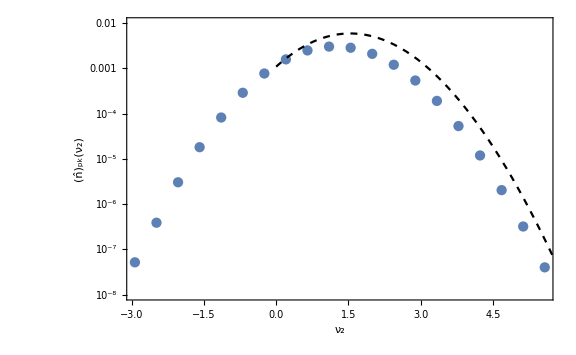

```mathematica
Show[ListLogPlot[nnu2Lat,Joined->False,FrameLabel->{{Subscript[OverHat[n], pk][Subscript[ν, 2]],None},{Subscript[ν, 2],σ^2==N[s2]}},PlotRange->{10^-8,10^-2},PlotLegends->Placed[PointLegend[{"lattice"},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.6,0.2}]],LogPlot[nnu2PT[nu2],{nu2,0,6},PlotStyle->{Dashed,Black},PlotLegends->Placed[LineLegend[{"peak theory"},LegendMarkerSize->20,LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.6,0.2}]]]
```

```mathematica
Cdata=Flatten[Cpeakdata[[All,All,5]]];
CnBins=20;
CbinSpec={Min[Cdata],Max[Cdata],(Max[Cdata]-Min[Cdata])/CnBins};
```

```mathematica
CbinEdges=HistogramList[Cdata,CbinSpec][[1]];
CbinCenters=MovingAverage[CbinEdges,2];
```

```mathematica
CPDFPerList=HistogramList[#[[All,5]],CbinSpec,"PDF"][[2]]&/@Cpeakdata;
```

```mathematica
CmeanPDF=Mean[CPDFPerList];
CsePDF=StandardDeviation[CPDFPerList]/Sqrt[Nsim];
```

```mathematica
nCLat=Table[{CbinCenters[[i]],(CmeanPDF[[i]]Length[Cdata])/(Nsim NL^3)±(CsePDF[[i]]Length[Cdata])/(Nsim NL^3)},{i,CnBins}];
```

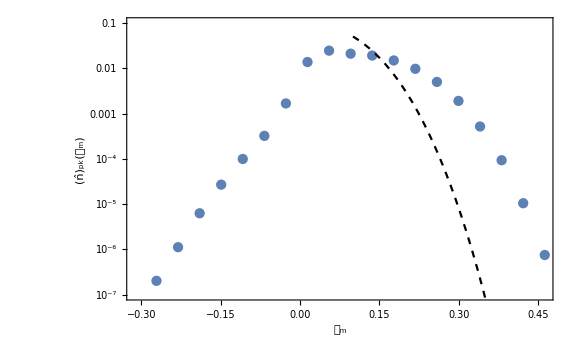

```mathematica
Show[ListLogPlot[nCLat,Joined->False,FrameLabel->{{Subscript[OverHat[n], pk][Subscript[𝒞, "m"]],None},{Subscript[𝒞, "m"],σ^2==N[s2]}},PlotLegends->Placed[PointLegend[{"lattice"},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.6,0.2}],PlotRange->{10^-7,10^-1}],
LogPlot[nCptint[Cm],{Cm,0.1,0.6},PlotStyle->{Black,Dashed},PlotLegends->Placed[LineLegend[{"peak theory"},LegendMarkerSize->20,LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.6,0.2}]]]
```

## Lognormal σ^2=1

```mathematica
npeak=32;
NL=512;
As=10^-2;(*3.625 10^-3;*)
```

```mathematica
kpeak=2π npeak/NL
```

π/8

```mathematica
s2=1;
```

```mathematica
σ1=Sqrt[E^(2 n^2 s2)kpeak^(2n)]/.{n->1};
σ2=Sqrt[E^(2 n^2 s2)kpeak^(2n)]/.{n->2};
σ3=Sqrt[E^(2 n^2 s2)kpeak^(2n)]/.{n->3};
σ4=Sqrt[E^(2 n^2 s2)kpeak^(2n)]/.{n->4};
```

### peak theory

```mathematica
calPz[lnk_]=1/Sqrt[2π s2] Exp[-lnk^2/(2s2)];
```

```mathematica
R3=Sqrt[3] σ3/σ4
```

(8 √3)/(ⅇ^7 π)

```mathematica
γn=E^(-2s2)
```

1/ⅇ^2

```mathematica
ψ1[x_]:=kpeak^2/σ1^2 NIntegrate[E^(2lnk)calPz[lnk]Sinc[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30,MaxRecursion->20]
ψ2[x_]:=kpeak^4/σ2^2 NIntegrate[E^(4lnk)calPz[lnk]Sinc[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30,MaxRecursion->20]
ψ1p[x_]:=kpeak^2/σ1^2 NIntegrate[E^(3lnk)calPz[lnk]Sinc'[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30,MaxRecursion->20]
ψ2p[x_]:=kpeak^4/σ2^2 NIntegrate[E^(5lnk)calPz[lnk]Sinc'[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30,MaxRecursion->20]
ψ1pp[x_]:=kpeak^2/σ1^2 NIntegrate[E^(4lnk)calPz[lnk]Sinc''[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30,MaxRecursion->20]
ψ2pp[x_]:=kpeak^4/σ2^2 NIntegrate[E^(6lnk)calPz[lnk]Sinc''[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30,MaxRecursion->20]
```

```mathematica
AbsoluteTiming[
ψ1List=ParallelTable[{x,ψ1[x]//Quiet},{x,10^-2,5,10^-2}];
ψ1pList=ParallelTable[{x,ψ1p[x]//Quiet},{x,10^-2,5,10^-2}];
ψ1ppList=ParallelTable[{x,ψ1pp[x]//Quiet},{x,10^-2,5,10^-2}];
ψ2List=ParallelTable[{x,ψ2[x]//Quiet},{x,10^-2,5,10^-2}];
ψ2pList=ParallelTable[{x,ψ2p[x]//Quiet},{x,10^-2,5,10^-2}];
ψ2ppList=ParallelTable[{x,ψ2pp[x]//Quiet},{x,10^-2,5,10^-2}];]
```

{353.464,Null}

```mathematica
ψ1int[x_]=Interpolation[ψ1List][x];
ψ1pint[x_]=Interpolation[ψ1pList][x];
ψ1ppint[x_]=Interpolation[ψ1ppList][x];
ψ2int[x_]=Interpolation[ψ2List][x];
ψ2pint[x_]=Interpolation[ψ2pList][x];
ψ2ppint[x_]=Interpolation[ψ2ppList][x];
```

```mathematica
ζx[x_,k3t_]=(1/(1-γn^2)(ψ1int[x]-1/3 R3^2 σ2^2/σ1^2 ψ2int[x])-k3t^2/(γn(1-γn^2))(γn^2 ψ1int[x]-1/3 R3^2 σ2^2/σ1^2 ψ2int[x]));
ζp[x_,k3t_]=(1/(1-γn^2)(ψ1pint[x]-1/3 R3^2 σ2^2/σ1^2 ψ2pint[x])-k3t^2/(γn(1-γn^2))(γn^2 ψ1pint[x]-1/3 R3^2 σ2^2/σ1^2 ψ2pint[x]));
ζpp[x_,k3t_]=(1/(1-γn^2)(ψ1ppint[x]-1/3 R3^2 σ2^2/σ1^2 ψ2ppint[x])-k3t^2/(γn(1-γn^2))(γn^2 ψ1ppint[x]-1/3 R3^2 σ2^2/σ1^2 ψ2ppint[x]));
```

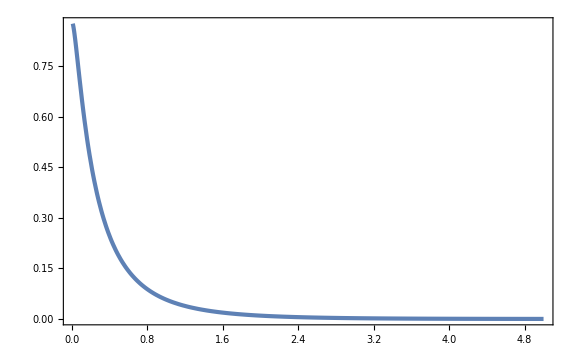

```mathematica
Plot[ζx[x,1],{x,0.01,5},PlotRange->Full]
```

```mathematica
CmCond[x_,k3t_]=(ζp[x,k3t]+x ζpp[x,k3t])/x^3;
```

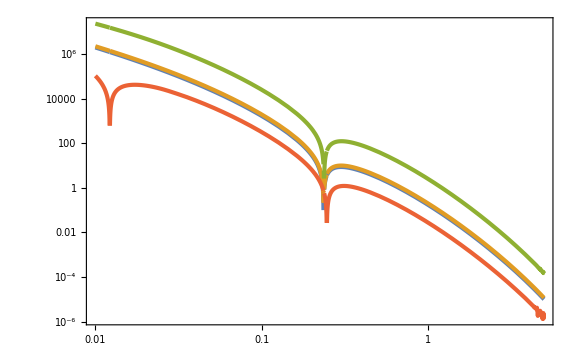

```mathematica
LogLogPlot[{Abs[CmCond[x,1]],Abs[CmCond[x,10^-2]],Abs[CmCond[x,10]],Abs[CmCond[x,2.9]]},{x,10^-2,5}]
```

```mathematica
xmList=ParallelTable[{10^lnk3t,x/.FindRoot[CmCond[x,10^lnk3t]==0,{x,(*Min[1/(2 10^lnk3t),0.1]*)0.011},WorkingPrecision->30]//Quiet},{lnk3t,-2,2,10^-2}];
```

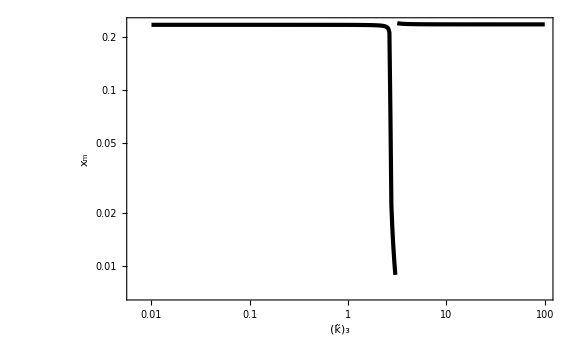

```mathematica
ListLogLogPlot[xmList,PlotRange->Full,FrameLabel->{Subscript[OverTilde[k], 3],Subscript[x, "m"]},PlotStyle->{Black,AbsoluteThickness[3]}]
```

```mathematica
xmint[k3t_]=Interpolation[xmList][k3t];
```

```mathematica
nu2inCk[Cm_,k3t_]=(Sqrt[1-3/2 Cm]-1)/(xmint[k3t] σ1^2/σ2 Sqrt[As]ζp[xmint[k3t],k3t]);
dnu2dCm[Cm_,k3t_]=D[nu2inCk[Cm,k3t], Cm]//Simplify;
```

```mathematica
f[x_]=1/2 x(x^2-3)(Erf[1/2 Sqrt[5/2]x]+Erf[Sqrt[5/2]x])+Sqrt[2/(5π)]((8/5+31/4 x^2)Exp[-5/8 x^2]+(-8/5+1/2 x^2)Exp[-5/2 x^2]);
P13[ν_,ξ_]=1/(2π Sqrt[1-γn^2])Exp[-1/2(ν^2+(ξ-γn ν)^2/(1-γn^2))];
npkPT[nu2_,k3t_]=2/(6π)^(3/2)(σ4/σ3)^3 nu2 k3t f[nu2 k3t^2]P13[nu2,nu2 k3t^2];
```

```mathematica
nCpt[Cm_]:=NIntegrate[npkPT[nu2inCk[Cm,k3t],k3t]Abs[dnu2dCm[Cm,k3t]],{k3t,1/10,1}(*,WorkingPrecision->30,MaxRecursion->12*)]
```

```mathematica
nCpt[2/10]
```

2.10425×10^-216

```mathematica
LogLogPlot[npkPT[nu2inCk[Cm,k3t],k3t]Abs[dnu2dCm[Cm,k3t]]/.{Cm->3/10},{k3t,1/20,1},WorkingPrecision->30]
```

General::munfl: Exp[-1263.45] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1263.46] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics-

```mathematica
nCpt[1/10]
```

2.09575×10^-46

```mathematica
nCptList=ParallelTable[{Cm,nCpt[Cm]},{Cm,10^-1,6/10,10^-2}];//AbsoluteTiming
```

{115.571,Null}

```mathematica
nCptint[Cm_]=Interpolation[nCptList][Cm];
```

### direct sampling

```mathematica
Nsim=1;
```

```mathematica
Lpeakdata=Table[Import["data/LN_Lpeak_0,1_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_"<>ToString[i]<>".csv"],{i,0,Nsim-1}];
```

```mathematica
HighLdata=Table[Select[Lpeakdata[[i]],#[[4]]>4σ2&],{i,Nsim}];
```

```mathematica
Cpeakdata=Table[Import["data/LN_Cpeak_0,1_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_"<>ToString[i]<>".csv"],{i,0,Nsim-1}];
```

```mathematica
HighCdata=Table[Select[Cpeakdata[[i]],#[[5]]>0.45&],{i,Nsim}];
```

```mathematica
matchQ[a_,b_]:=Max[Abs[a[[{1,2,3}]]-b[[{2,3,4}]]]]<=1;
```

```mathematica
onlyInC=Table[Select[HighCdata[[i]],Function[b,!AnyTrue[HighLdata[[i]],matchQ[#,b]&]]],{i,Nsim}];
```

```mathematica
γ3=σ3^2/(σ2 σ4);
f[x_]=1/2 x(x^2-3)(Erf[1/2 Sqrt[5/2]x]+Erf[Sqrt[5/2]x])+Sqrt[2/(5π)]((8/5+31/4 x^2)Exp[-5/8 x^2]+(-8/5+1/2 x^2)Exp[-5/2 x^2]);
P13[ν_,ξ_]=1/(2π Sqrt[1-γ3^2])Exp[-1/2(ν^2+(ξ-γ3 ν)^2/(1-γ3^2))];
npkPT[nu2_,k3t_]=2/(6π)^(3/2)σ4^3/σ3^3 nu2 k3t f[nu2 k3t^2]P13[nu2,nu2 k3t^2];
nnu2PT[nu2_]:=NIntegrate[npkPT[nu2,k3t],{k3t,0,∞}];
```

```mathematica
nudata=Flatten[Lpeakdata[[All,All,4]]/σ2];
nunBins=20;
nubinSpec={Min[nudata],Max[nudata],(Max[nudata]-Min[nudata])/nunBins};
```

```mathematica
nubinEdges=HistogramList[nudata,nubinSpec][[1]];
nubinCenters=MovingAverage[nubinEdges,2];
```

```mathematica
nuPDFPerList=HistogramList[(#[[All,4]])/σ2,nubinSpec,"PDF"][[2]]&/@Lpeakdata;
```

```mathematica
numeanPDF=Mean[nuPDFPerList];
(*nusePDF=StandardDeviation[nuPDFPerList]/Sqrt[Nsim];*)
```

```mathematica
nnu2Lat=Table[{nubinCenters[[i]],(numeanPDF[[i]]Length[nudata])/(Nsim NL^3)(*±(nusePDF[[i]]Length[nudata])/(Nsim NL^3)*)},{i,nunBins}];
```

```mathematica
Show[ListLogPlot[nnu2Lat,Joined->False,FrameLabel->{{Subscript[OverHat[n], pk][Subscript[ν, 2]],None},{Subscript[ν, 2],σ^2==N[s2]}}(*,PlotRange->{10^-9,10^-3}*),PlotLegends->Placed[PointLegend[{"lattice"},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.6,0.2}]],LogPlot[nnu2PT[nu2],{nu2,0,6},PlotStyle->{Dashed,Black},PlotLegends->Placed[LineLegend[{"peak theory"},LegendMarkerSize->20,LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.6,0.2}]]]
```

-Graphics-

```mathematica
Cdata=Flatten[Cpeakdata[[All,All,5]]];
CnBins=20;
CbinSpec={Min[Cdata],Max[Cdata],(Max[Cdata]-Min[Cdata])/CnBins};
```

```mathematica
CbinEdges=HistogramList[Cdata,CbinSpec][[1]];
CbinCenters=MovingAverage[CbinEdges,2];
```

```mathematica
CPDFPerList=HistogramList[#[[All,5]],CbinSpec,"PDF"][[2]]&/@Cpeakdata;
```

```mathematica
CmeanPDF=Mean[CPDFPerList];
(*CsePDF=StandardDeviation[CPDFPerList]/Sqrt[Nsim];*)
```

```mathematica
nCLat=Table[{CbinCenters[[i]],(CmeanPDF[[i]]Length[Cdata])/(Nsim NL^3)(*±(CsePDF[[i]]Length[Cdata])/(Nsim NL^3)*)},{i,CnBins}];
```

```mathematica
Show[ListLogPlot[nCLat,Joined->False,FrameLabel->{{Subscript[OverHat[n], pk][Subscript[𝒞, "m"]],None},{Subscript[𝒞, "m"],σ^2==N[s2]}},PlotLegends->Placed[PointLegend[{"lattice"},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.6,0.2}]],
LogPlot[nCptint[Cm],{Cm,0.1,0.6},PlotStyle->{Black,Dashed},PlotLegends->Placed[LineLegend[{"peak theory"},LegendMarkerSize->20,LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.6,0.2}]]]
```

-Graphics-

## Lognormal σ^2=0.1 kUV

```mathematica
npeak=32;
NL=512;
As=10^-2;(*3.625 10^-3;*)
```

```mathematica
kpeak=2π npeak/NL
```

π/8

```mathematica
s2=10^-1;
```

### peak theory

```mathematica
calPz[lnk_]=1/Sqrt[2π s2] Exp[-lnk^2/(2s2)];
```

```mathematica
f[x_]=1/2 x(x^2-3)(Erf[1/2 Sqrt[5/2]x]+Erf[Sqrt[5/2]x])+Sqrt[2/(5π)]((8/5+31/4 x^2)Exp[-5/8 x^2]+(-8/5+1/2 x^2)Exp[-5/2 x^2]);
```

```mathematica
kUVs=5;
```

```mathematica
AbsoluteTiming[
σ1=Sqrt[kpeak^2 NIntegrate[E^(2 lnk)calPz[lnk],{lnk,-∞,Log[kUVs]}]];
σ2=Sqrt[kpeak^4 NIntegrate[E^(4 lnk)calPz[lnk],{lnk,-∞,Log[kUVs]}]];
σ3=Sqrt[kpeak^6 NIntegrate[E^(6 lnk)calPz[lnk],{lnk,-∞,Log[kUVs]}]];
σ4=Sqrt[kpeak^8 NIntegrate[E^(8 lnk)calPz[lnk],{lnk,-∞,Log[kUVs]}]];
R3=Sqrt[3] σ3/σ4;
γ3=σ3^2/(σ2 σ4);
ψ1[x_]:=kpeak^2/σ1^2 NIntegrate[E^(2lnk)calPz[lnk]Sinc[E^lnk x],{lnk,-∞,Log[kUVs]},Method->"GaussKronrodRule",WorkingPrecision->30];
ψ2[x_]:=kpeak^4/σ2^2 NIntegrate[E^(4lnk)calPz[lnk]Sinc[E^lnk x],{lnk,-∞,Log[kUVs]},Method->"GaussKronrodRule",WorkingPrecision->30];
ψ1p[x_]:=kpeak^2/σ1^2 NIntegrate[E^(3lnk)calPz[lnk]Sinc'[E^lnk x],{lnk,-∞,Log[kUVs]},Method->"GaussKronrodRule",WorkingPrecision->30];
ψ2p[x_]:=kpeak^4/σ2^2 NIntegrate[E^(5lnk)calPz[lnk]Sinc'[E^lnk x],{lnk,-∞,Log[kUVs]},Method->"GaussKronrodRule",WorkingPrecision->30];
ψ1pp[x_]:=kpeak^2/σ1^2 NIntegrate[E^(4lnk)calPz[lnk]Sinc''[E^lnk x],{lnk,-∞,Log[kUVs]},Method->"GaussKronrodRule",WorkingPrecision->30];
ψ2pp[x_]:=kpeak^4/σ2^2 NIntegrate[E^(6lnk)calPz[lnk]Sinc''[E^lnk x],{lnk,-∞,Log[kUVs]},Method->"GaussKronrodRule",WorkingPrecision->30];
ψ1List=Table[{x,ψ1[x]},{x,10^-2,10,10^-2}];
ψ1pList=Table[{x,ψ1p[x]},{x,10^-2,10,10^-2}];
ψ1ppList=Table[{x,ψ1pp[x]},{x,10^-2,10,10^-2}];
ψ2List=Table[{x,ψ2[x]},{x,10^-2,10,10^-2}];
ψ2pList=Table[{x,ψ2p[x]},{x,10^-2,10,10^-2}];
ψ2ppList=Table[{x,ψ2pp[x]},{x,10^-2,10,10^-2}];
ψ1int[x_]=Interpolation[ψ1List][x];
ψ1pint[x_]=Interpolation[ψ1pList][x];
ψ1ppint[x_]=Interpolation[ψ1ppList][x];
ψ2int[x_]=Interpolation[ψ2List][x];
ψ2pint[x_]=Interpolation[ψ2pList][x];
ψ2ppint[x_]=Interpolation[ψ2ppList][x];
ζx[x_,k3t_]=(1/(1-γ3^2)(ψ1int[x]-1/3 R3^2 σ2^2/σ1^2 ψ2int[x])-k3t^2/(γ3(1-γ3^2))(γ3^2 ψ1int[x]-1/3 R3^2 σ2^2/σ1^2 ψ2int[x]));
ζp[x_,k3t_]=(1/(1-γ3^2)(ψ1pint[x]-1/3 R3^2 σ2^2/σ1^2 ψ2pint[x])-k3t^2/(γ3(1-γ3^2))(γ3^2 ψ1pint[x]-1/3 R3^2 σ2^2/σ1^2 ψ2pint[x]));
ζpp[x_,k3t_]=(1/(1-γ3^2)(ψ1ppint[x]-1/3 R3^2 σ2^2/σ1^2 ψ2ppint[x])-k3t^2/(γ3(1-γ3^2))(γ3^2 ψ1ppint[x]-1/3 R3^2 σ2^2/σ1^2 ψ2ppint[x]));
CmCond[x_,k3t_]=(ζp[x,k3t]+x ζpp[x,k3t])/x^3;
xmList=Table[{10^lnk3t,x/.FindRoot[CmCond[x,10^lnk3t]==0,{x,Min[1/(2 10^lnk3t),0.05]},WorkingPrecision->30]//Quiet},{lnk3t,-2,2,10^-2}];
xmint[k3t_]=Interpolation[xmList][k3t];
nu2inCk[Cm_,k3t_]=(Sqrt[1-3/2 Cm]-1)/(xmint[k3t] σ1^2/σ2^2 Sqrt[As]ζp[xmint[k3t],k3t]);
dnu2dCm[Cm_,k3t_]=D[nu2inCk[Cm,k3t], Cm]//Simplify;
P13[ν_,ξ_]=1/(2π Sqrt[1-γ3^2])Exp[-1/2(ν^2+(ξ-γ3 ν)^2/(1-γ3^2))];
npkPT[nu2_,k3t_]=2/(6π)^(3/2)(σ4/σ3)^3 nu2 k3t f[nu2 k3t^2]P13[nu2,nu2 k3t^2];
nCpt[Cm_]:=NIntegrate[npkPT[nu2inCk[Cm,k3t],k3t]Abs[dnu2dCm[Cm,k3t]],{k3t,2/5,2}(*,WorkingPrecision->30,MaxRecursion->12*)];
nCptList=Table[{Cm,nCpt[Cm]},{Cm,10^-1,6/10,10^-2}];
]
```

{5676.84,Null}

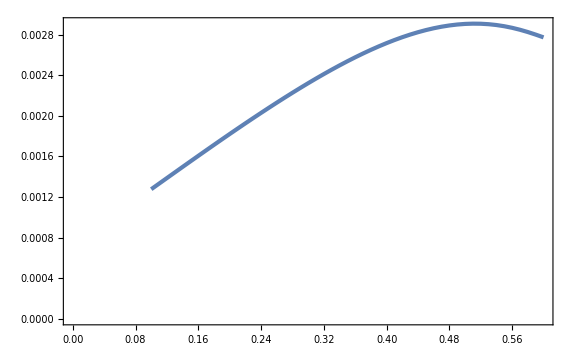

```mathematica
ListPlot[nCptList]
```

```mathematica
nCptint[Cm_]=Interpolation[nCptList][Cm];
```

### direct sampling

```mathematica
Nsim=10;
```

```mathematica
Lpeakdata=Table[Import["data/LN_Lpeak_0,1_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_"<>ToString[i]<>".csv"],{i,0,Nsim-1}];
```

```mathematica
HighLdata=Table[Select[Lpeakdata[[i]],#[[4]]>4σ2&],{i,Nsim}];
```

```mathematica
Cpeakdata=Table[Import["data/LN_Cpeak_0,1_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_"<>ToString[i]<>".csv"],{i,0,Nsim-1}];
```

```mathematica
HighCdata=Table[Select[Cpeakdata[[i]],#[[5]]>0.45&],{i,Nsim}];
```

```mathematica
matchQ[a_,b_]:=Max[Abs[a[[{1,2,3}]]-b[[{2,3,4}]]]]<=1;
```

```mathematica
onlyInC=Table[Select[HighCdata[[i]],Function[b,!AnyTrue[HighLdata[[i]],matchQ[#,b]&]]],{i,Nsim}];
```

```mathematica
γ3=σ3^2/(σ2 σ4);
f[x_]=1/2 x(x^2-3)(Erf[1/2 Sqrt[5/2]x]+Erf[Sqrt[5/2]x])+Sqrt[2/(5π)]((8/5+31/4 x^2)Exp[-5/8 x^2]+(-8/5+1/2 x^2)Exp[-5/2 x^2]);
P13[ν_,ξ_]=1/(2π Sqrt[1-γ3^2])Exp[-1/2(ν^2+(ξ-γ3 ν)^2/(1-γ3^2))];
npkPT[nu2_,k3t_]=2/(6π)^(3/2)σ4^3/σ3^3 nu2 k3t f[nu2 k3t^2]P13[nu2,nu2 k3t^2];
nnu2PT[nu2_]:=NIntegrate[npkPT[nu2,k3t],{k3t,0,∞}];
```

```mathematica
nudata=Flatten[Lpeakdata[[All,All,4]]/σ2];
nunBins=20;
nubinSpec={Min[nudata],Max[nudata],(Max[nudata]-Min[nudata])/nunBins};
```

```mathematica
nubinEdges=HistogramList[nudata,nubinSpec][[1]];
nubinCenters=MovingAverage[nubinEdges,2];
```

```mathematica
nuPDFPerList=HistogramList[(#[[All,4]])/σ2,nubinSpec,"PDF"][[2]]&/@Lpeakdata;
```

```mathematica
numeanPDF=Mean[nuPDFPerList];
nusePDF=StandardDeviation[nuPDFPerList]/Sqrt[Nsim];
```

```mathematica
nnu2Lat=Table[{nubinCenters[[i]],(numeanPDF[[i]]Length[nudata])/(Nsim NL^3)±(nusePDF[[i]]Length[nudata])/(Nsim NL^3)},{i,nunBins}];
```

```mathematica
Show[ListLogPlot[nnu2Lat,Joined->False,FrameLabel->{{Subscript[OverHat[n], pk][Subscript[ν, 2]],None},{Subscript[ν, 2],σ^2==N[s2]}}(*,PlotRange->{10^-9,10^-3}*),PlotLegends->Placed[PointLegend[{"lattice"},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.6,0.2}]],LogPlot[nnu2PT[nu2],{nu2,0,6},PlotStyle->{Dashed,Black},PlotLegends->Placed[LineLegend[{"peak theory"},LegendMarkerSize->20,LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.6,0.2}]]]
```

-Graphics-

```mathematica
Cdata=Flatten[Cpeakdata[[All,All,5]]];
CnBins=20;
CbinSpec={Min[Cdata],Max[Cdata],(Max[Cdata]-Min[Cdata])/CnBins};
```

```mathematica
CbinEdges=HistogramList[Cdata,CbinSpec][[1]];
CbinCenters=MovingAverage[CbinEdges,2];
```

```mathematica
CPDFPerList=HistogramList[#[[All,5]],CbinSpec,"PDF"][[2]]&/@Cpeakdata;
```

```mathematica
CmeanPDF=Mean[CPDFPerList];
CsePDF=StandardDeviation[CPDFPerList]/Sqrt[Nsim];
```

```mathematica
nCLat=Table[{CbinCenters[[i]],(CmeanPDF[[i]]Length[Cdata])/(Nsim NL^3)±(CsePDF[[i]]Length[Cdata])/(Nsim NL^3)},{i,CnBins}];
```

```mathematica
Show[ListLogPlot[nCLat,Joined->False,FrameLabel->{{Subscript[OverHat[n], pk][Subscript[𝒞, "m"]],None},{Subscript[𝒞, "m"],σ^2==N[s2]}},PlotLegends->Placed[PointLegend[{"lattice"},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.6,0.2}]],
LogPlot[nCptint[Cm],{Cm,0.1,0.6},PlotStyle->{Black,Dashed},PlotLegends->Placed[LineLegend[{"peak theory"},LegendMarkerSize->20,LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.6,0.2}]]]
```

-Graphics-

## Bias-profile Peak Theory

σ.b2=0.1 の compaction peak 数密度を、typical profile の PT (β=0) ではなく、bias profile 方向の profile 揺らぎ β~N(0,1) を入れた PT (bias-profile PT; peak_theory2.nb の同名セクションと同じ手法) で direct sampling と比べる。peak の拘束 (ν₂, k̃₃) を満たす typical profile に bias profile の ⊥ 成分 β ŵ を足し、n(C_m)=∫dν dk̃ dβ n_pk(ν,k̃) φ(β) δ(C_max(ν,k̃,β)−C_m) を計算する。(A) A_s=1e-2, NL=512, npeak=32: 全 compaction peak (Cpeak: 空間 3 次元 + 半径方向の極大) の n̂_pk(C_m)。(B) A_s=5e-3, NL=256, npeak=16: Laplacian peak (ν₂≥3) の中心での C_max の分布 (Cprof; Cmax_c が peak 中心、Cmax_n が 3×3×3 近傍の最大)。(B) は PT と同じ「peak 中心の球対称 profile」の量、(A) は peak 位置のずれも含む量。図の黒破線: typical PT (β=0)、赤実線: bias-profile PT (連続 x で C 最大)、赤点線: bias-profile PT (格子と同じ整数半径のみで C 最大)、青点: direct sampling。

```mathematica
bpcf2=Compile[{{nu,_Real},{kG,_Real,1},{bG,_Real,1},{V2,_Real,1},{V4,_Real,1},{Vw,_Real,1},{V2d,_Real,1},{V4d,_Real,1},{Vwd,_Real,1}},Table[Module[{q=nu kG⟦i⟧^2,b=bG⟦j⟧,best=-10.,bd=-10.,v=0.,c=0.},Do[v=nu V2⟦l⟧+q V4⟦l⟧+b Vw⟦l⟧;c=(2. (1.-(1.+v)^2))/3.;If[c>best,best=c],{l,Length[V2]}];Do[v=nu V2d⟦l⟧+q V4d⟦l⟧+b Vwd⟦l⟧;c=(2. (1.-(1.+v)^2))/3.;If[c>bd,bd=c],{l,Length[V2d]}];{best,bd}],{i,Length[kG]},{j,Length[bG]}]];bpCompute[As_,np_,NL_,numin_,numax_,nbin_]:=Module[{s2=1/10,kp=(2 π np)/NL,sg,g,f,P13,npk,dl=0.01,lk,Pz,sq,Eg,Pinv,ub0,wp,wh,Vs,xc,xd,V2,V4,Vw,W2,W4,Ww,nuG,kG,bG,res,nk,phi,w,binf,cc,ib0,nuM,bM,out},sg[n_]:=√(Exp[2 n^2 s2] kp^(2 n));g=Exp[-2 s2];f[x_]:=1/2 x (x^2-3) (Erf[1/2 √(5/2) x]+Erf[√(5/2) x])+√(2/(5 π)) ((8/5+(31 x^2)/4) Exp[-(5 x^2)/8]+(-8/5+x^2/2) Exp[-(5 x^2)/2]);P13[nu_,xi_]:=Exp[-1/2 (nu^2+(xi-g nu)^2/(1-g^2))]/(2 π √(1-g^2));npk[nu_,k_]:=(2 (sg[4]/sg[3])^3 nu k f[nu k^2] P13[nu,nu k^2])/(6 π)^(3/2);lk=Range[-2.5,2.5,dl];Pz=PDF[NormalDistribution[0,√s2],lk];sq=√(As Pz dl);Eg={kp^2 Exp[2 lk] √(Pz dl),kp^4 Exp[4 lk] √(Pz dl)};Pinv=Transpose[Eg].Inverse[Eg.Transpose[Eg]];ub0=√dl Pz;wp=ub0-Pinv.(Eg.ub0);wh=wp/Norm[wp];Vs[xs_]:=Module[{B},B=Table[sq Exp[lk] x (Cos[Exp[lk] x]/(Exp[lk] x)-Sin[Exp[lk] x]/(Exp[lk] x)^2),{x,xs}];{sg[2] B.Pinv⟦All,1⟧,sg[4] B.Pinv⟦All,2⟧,B.wh}];xc=Range[0.01,8,0.01];xd=kp Range[1,Floor[5/kp]];{V2,V4,Vw}=Vs[xc];{W2,W4,Ww}=Vs[xd];nuG=Range[numin+0.025,numax,0.05];kG=Range[0.2,2,0.025];bG=Range[-5,9,0.1];res=Table[bpcf2[nu,kG,bG,V2,V4,Vw,W2,W4,Ww],{nu,nuG}];nk=Table[npk[nu,k],{nu,nuG},{k,kG}];phi=PDF[NormalDistribution[0,1],bG];w=Table[nk⟦i,j⟧ 0.05 0.025 phi⟦l⟧ 0.1,{i,Length[nuG]},{j,Length[kG]},{l,Length[bG]}];binf[C_,ww_]:=Module[{idx=Developer`ToPackedArray[Floor[(Flatten[C]-0.05)/0.025]+1],v=Developer`ToPackedArray[Flatten[ww]]},Table[v.(1-Unitize[idx-i]),{i,nbin}]/0.025];cc=Range[0.05,0.05+0.025 (nbin-1),0.025]+0.0125;ib0=First[Flatten[Position[bG,_?(Abs[#1]<1/10^9&)]]];nuM=Table[nuG⟦i⟧,{i,Length[nuG]},{j,Length[kG]},{l,Length[bG]}];bM=Table[bG⟦l⟧,{i,Length[nuG]},{j,Length[kG]},{l,Length[bG]}];Association["C"->cc,"bias"->binf[res⟦All,All,All,1⟧,w],"biasD"->binf[res⟦All,All,All,2⟧,w],"pt0"->binf[res⟦All,All,{ib0},1⟧,w⟦All,All,{ib0}⟧/(0.1 phi⟦ib0⟧)],"pt0D"->binf[res⟦All,All,{ib0},2⟧,w⟦All,All,{ib0}⟧/(0.1 phi⟦ib0⟧)],"meanBeta"->binf[res⟦All,All,All,1⟧,w bM]/(binf[res⟦All,All,All,1⟧,w]+1/10^300),"meanNu"->binf[res⟦All,All,All,1⟧,w nuM]/(binf[res⟦All,All,All,1⟧,w]+1/10^300),"nPT"->Total[nk,2] 0.05 0.025]]
```

```mathematica
tA=AbsoluteTiming[bpA=bpCompute[1/100,32,512,0.075,12,18]]⟦1⟧;tB=AbsoluteTiming[bpB=bpCompute[1/200,16,256,3,14,24]]⟦1⟧;{tA,tB}
```

General::munfl: Exp[-722.5] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-739.6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-719.759] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{169.237,156.359}

```mathematica
cpkA=Table[Import["data/As=1e-2/LN_Cpeak_0,1_512_32_"<>ToString[i]<>".csv"],{i,0,9}];latAh=Table[BinCounts[cpkA⟦i,All,5⟧,{0.05,0.5,0.025}]/(512^3 0.025),{i,10}];latA=Transpose[{bpA["C"],Mean[latAh],StandardDeviation[latAh]/(√10)}];cprofB=Join@@Table[Import["data/As=5e-3/LN_Cprof_0,1_256_16_"<>ToString[i]<>".csv"],{i,0,99}];latBc=BinCounts[cprofB⟦All,6⟧,{0.05,0.65,0.025}]/(100 256^3 0.025);latBn=BinCounts[cprofB⟦All,8⟧,{0.05,0.65,0.025}]/(100 256^3 0.025);{Length[cprofB]/(100. 256^3),bpB["nPT"]}
```

{0.000093559,0.000120742}

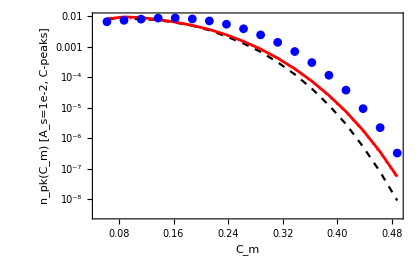
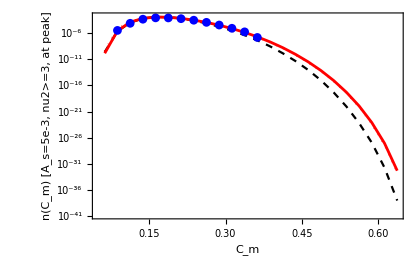

```mathematica
plotCmp[C_,curves_,pts_,ylab_]:=Show[ListLogPlot[curves,Joined->True,PlotStyle->{{Black,Dashed},{Red,AbsoluteThickness[2]},{Red,Dotted}},PlotRange->{{0.05,Max[C]},All}],ListLogPlot[pts,Joined->False,PlotStyle->{Blue,PointSize[0.015]}],Frame->True,FrameLabel->{"C_m",ylab},ImageSize->420];{plotCmp[bpA["C"],{Transpose[{bpA["C"],bpA["pt0"]}],Transpose[{bpA["C"],bpA["bias"]}],Transpose[{bpA["C"],bpA["biasD"]}]},Select[latA⟦All,{1,2}⟧,#1⟦2⟧>0&],"n_pk(C_m) [A_s=1e-2, C-peaks]"],plotCmp[bpB["C"],{Transpose[{bpB["C"],bpB["pt0"]}],Transpose[{bpB["C"],bpB["bias"]}],Transpose[{bpB["C"],bpB["biasD"]}]},Select[Transpose[{bpB["C"],latBc}],#1⟦2⟧>0&],"n(C_m) [A_s=5e-3, nu2>=3, at peak]"]}
```

```mathematica
ratioTab[C_,lat_,pt0_,bias_]:=Select[Transpose[{C,lat,pt0,bias,lat/pt0,lat/bias}],#1⟦2⟧>0&&#1⟦1⟧≥0.1&];{Grid[Prepend[N[ratioTab[bpA["C"],latA⟦All,2⟧,bpA["pt0"],bpA["bias"]]],{"C_m","lattice","PT (typical)","bias-PT","lat/PT","lat/bias-PT"}],Frame->All],Grid[Prepend[N[ratioTab[bpB["C"],latBc,bpB["pt0"],bpB["bias"]]],{"C_m","lattice (centre)","PT (typical)","bias-PT","lat/PT","lat/bias-PT"}],Frame->All]}
```

{C_m | lattice | PT (typical) | bias-PT | lat/PT | lat/bias-PT
0.1125 | 0.00805792 | 0.00817932 | 0.00907978 | 0.985158 | 0.887457
0.1375 | 0.00872353 | 0.00751255 | 0.00785615 | 1.16119 | 1.11041
0.1625 | 0.00882411 | 0.00620463 | 0.00645321 | 1.42218 | 1.3674
0.1875 | 0.0081749 | 0.00491347 | 0.00504148 | 1.66377 | 1.62153
0.2125 | 0.00703022 | 0.00348249 | 0.00368283 | 2.01873 | 1.90892
0.2375 | 0.00549451 | 0.00217712 | 0.00246709 | 2.52375 | 2.22712
0.2625 | 0.00389391 | 0.00128608 | 0.00150488 | 3.02774 | 2.58752
0.2875 | 0.0024592 | 0.000683852 | 0.000844213 | 3.5961 | 2.91301
0.3125 | 0.00139841 | 0.000311574 | 0.000423073 | 4.48823 | 3.30538
0.3375 | 0.000698894 | 0.000124925 | 0.000190379 | 5.5945 | 3.67107
0.3625 | 0.000303984 | 0.0000425099 | 0.0000747622 | 7.1509 | 4.06601
0.3875 | 0.000116736 | 0.0000121491 | 0.0000254602 | 9.60859 | 4.58502
0.4125 | 0.0000379086 | 2.912×10^-6 | 7.50216×10^-6 | 13.018 | 5.05302
0.4375 | 9.38773×10^-6 | 5.29012×10^-7 | 1.82606×10^-6 | 17.7458 | 5.14096
0.4625 | 2.23517×10^-6 | 7.92935×10^-8 | 3.59636×10^-7 | 28.1886 | 6.21511
0.4875 | 3.27826×10^-7 | 9.12933×10^-9 | 5.52421×10^-8 | 35.9091 | 5.93435,C_m | lattice (centre) | PT (typical) | bias-PT | lat/PT | lat/bias-PT
0.1125 | 0.0000870228 | 0.000119603 | 0.000147272 | 0.727597 | 0.590898
0.1375 | 0.000533271 | 0.000739624 | 0.000772509 | 0.721003 | 0.69031
0.1625 | 0.000974345 | 0.0014714 | 0.00135113 | 0.662189 | 0.721131
0.1875 | 0.000943995 | 0.00132842 | 0.0012479 | 0.710613 | 0.756466
0.2125 | 0.000673914 | 0.000767827 | 0.00077177 | 0.87769 | 0.873205
0.2375 | 0.00034101 | 0.000290778 | 0.000358848 | 1.17275 | 0.950291
0.2625 | 0.000132656 | 0.0000867404 | 0.000129063 | 1.52935 | 1.02784
0.2875 | 0.0000406027 | 0.0000188423 | 0.0000375996 | 2.15487 | 1.07987
0.3125 | 9.65595×10^-6 | 3.41456×10^-6 | 8.6392×10^-6 | 2.82788 | 1.11769
0.3375 | 1.97887×10^-6 | 4.62486×10^-7 | 1.58156×10^-6 | 4.27878 | 1.25122
0.3625 | 1.66893×10^-7 | 4.67634×10^-8 | 2.2151×10^-7 | 3.56888 | 0.753433}

```mathematica
Module[{s2=1/10,kp=π/8,sg,g,f,P13,npk,sig2,edges=Range[3,6.5,0.5],rows},sg[n_]:=√(Exp[2 n^2 s2] kp^(2 n));g=Exp[-2 s2];f[x_]:=1/2 x (x^2-3) (Erf[1/2 √(5/2) x]+Erf[√(5/2) x])+√(2/(5 π)) ((8/5+(31 x^2)/4) Exp[-(5 x^2)/8]+(-8/5+x^2/2) Exp[-(5 x^2)/2]);P13[nu_,xi_]:=Exp[-1/2 (nu^2+(xi-g nu)^2/(1-g^2))]/(2 π √(1-g^2));npk[nu_,k_]:=(2 (sg[4]/sg[3])^3 nu k f[nu k^2] P13[nu,nu k^2])/(6 π)^(3/2);sig2=sg[2];rows=Table[Module[{a=edges⟦i⟧,b=edges⟦i+1⟧,cnt,pt},cnt=Count[cprofB⟦All,4⟧/sig2,_?(a≤#1<b&)];pt=NIntegrate[npk[nu,k],{nu,a,b},{k,0.01,3}]/(b-a);{(a+b)/2,cnt,cnt/((100. 256^3) (b-a)),pt,cnt/(((100. 256^3) (b-a)) pt)}],{i,Length[edges]-1}];Grid[Prepend[N[rows],{"nu2","count","lattice n","PT n","lattice/PT"}],Frame->All]]
```

nu2 | count | lattice n | PT n | lattice/PT
3.25 | 117698. | 0.000140307 | 0.000175942 | 0.797463
3.75 | 31892. | 0.0000380182 | 0.0000523025 | 0.726891
4.25 | 6310. | 7.52211×10^-6 | 0.0000113022 | 0.665542
4.75 | 941. | 1.12176×10^-6 | 1.80521×10^-6 | 0.6214
5.25 | 110. | 1.3113×10^-7 | 2.158×10^-7 | 0.607648
5.75 | 14. | 1.66893×10^-8 | 1.94844×10^-8 | 0.856547
6.25 | 1. | 1.19209×10^-9 | 1.33748×10^-9 | 0.891299

結果。(B) peak 中心の C_m (ν₂≥3, A_s=5e-3): typical PT は C_m≳0.25 で lattice を過小評価する (lattice/PT = 1.5 (C_m=0.26), 2.8 (0.31), 4.3 (0.34))。bias-profile PT を使うと lattice/bias-PT = 1.03, 1.12, 1.25 (C_m=0.34 の統計誤差は 83 個で約 11%) となり、C_m=0.21–0.34 で lattice と 25% 以内で一致する。一方 C_m≲0.19 では PT・bias-PT とも lattice より 30–40% 多い (lattice/bias-PT = 0.6–0.8)。これは profile の問題ではなく、Laplacian peak の数密度自体が lattice で PT より少ないため (下の表: ν₂ ビン別 lattice/PT = 0.80 (ν₂=3.25), 0.73 (3.75), 0.67 (4.25), 0.62 (4.75), 0.61 (5.25)。ν₂≥3 の総数比は 0.78)。この不足を平均 ν₂ で補正すると、C_m=0.21–0.34 の lattice/bias-PT は ≈1.1–2.0 になり、bias 方向だけでは約 1.5–2 倍の超過が残る。(A) 全 compaction peak (A_s=1e-2): lattice/typical PT = 1.0 (C_m≲0.14), 2.0 (0.21), 4.5 (0.31), 13 (0.41), 36 (0.49) に対し、lattice/bias-PT = 1.9, 3.3, 5.1, 5.9 (同 C_m)。改善はするが 5–6 倍残る。(B) の 3×3×3 近傍最大 (Cmax_n) は peak 中心より更に大きく (lattice/bias-PT ≈ 1.1 (C_m=0.21) → 3.9 (0.34))、(A) の C-peak は空間位置についても最大化した量なので、残りは peak 位置のずれ (非球対称性) の寄与が大きいと考えられる。まとめ: bias profile の揺らぎを入れた PT は peak 中心の C_m 分布の高 C tail (typical PT の 2–4 倍の不足) をほぼ再現するが、σ.b2=0.1 の不一致の全部は説明しない。残りは (i) lattice の Laplacian peak 数密度が PT より少ないこと (ν₂=3→5 で 0.8→0.6 倍)、(ii) C-peak の位置ずれ、(iii) bias 方向以外の ⊥ 揺らぎ、であり、(i)(ii) は profile 揺らぎとは別の効果である。

Importance sampling との比較 (A_s=1e-2, NL=256, npeak=16)
IS (Gaussian_LN_GBC3: shell-wise にガウス平均をシフトし、尤度比 W で補正) で、direct sampling と同じ局所 compaction-peak 判定 (C0<C1>C2 かつ座標方向の極大) を原点近傍の窓 (33^3) に適用して n(C_m) を推定した。n(C_m)=Σ_{events in bin, |x|_inf<=m}/(N|R|)·W̄_bin/ΔC, W̄=exp(<lnW>+Var/2) (ビンごとの対数正規近似)。bias 強度 bc=1..8 (各 800 サンプル)。図: 黒四角=direct sampling (512,32; 10 box), 点=IS(m=1), 黒破線=PT (typical), 赤=PT (bias profile)。

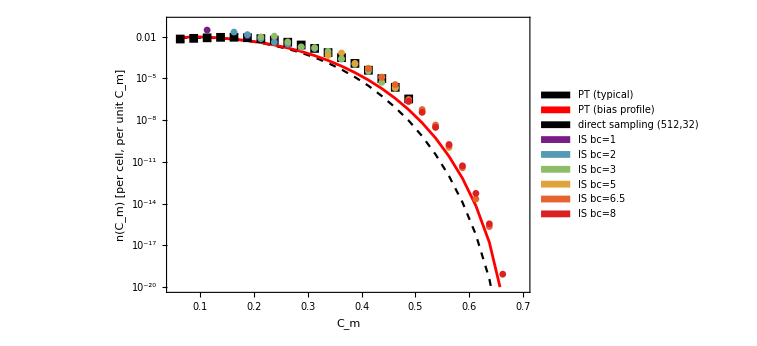

```mathematica
bpIS = bpCompute[1/100, 16, 256, 0.075, 14, 26];  (* NL=256, npeak=16: kp equal to (512,32) *)
isD = Rest[Import["data/As=1e-2/IS_As1e-2_nC.csv"]];  (* columns: bc, m, C, n, n_lo, n_hi, nev; m: origin cube |x|_inf<=m, m=1 plotted *)
isCol[bc_] := ColorData["Rainbow"][(Log[bc] - Log[1])/(Log[8] - Log[1])];
bcs = {1, 2, 3, 5, 6.5, 8};
gIS = Module[{C = bpIS["C"]},
 ListLogPlot[Join[{Transpose[{C, bpIS["pt0"]}], Transpose[{C, bpIS["bias"]}], Select[latA[[All, {1, 2}]], #[[2]] > 0 &]}, Table[Select[isD, #[[1]] == b && #[[2]] == 1 &][[All, {3, 4}]], {b, bcs}]],
  Joined -> Join[{True, True, False}, ConstantArray[False, 6]],
  PlotStyle -> Join[{{Black, Dashed}, {Red, AbsoluteThickness[2]}, {Black, PointSize[0.014]}}, Table[{isCol[b], PointSize[0.012]}, {b, bcs}]],
  PlotMarkers -> Join[{None, None, {"■", 9}}, Table[{"●", 7}, {6}]],
  Frame -> True, FrameLabel -> {"C_m", "n(C_m)  [per cell, per unit C_m]"}, PlotRange -> {{0.05, 0.7}, {10^-20, 0.1}}, ImageSize -> 560,
  PlotLegends -> SwatchLegend[Join[{Black, Red, Black}, Table[isCol[b], {b, bcs}]], Join[{"PT (typical)", "PT (bias profile)", "direct sampling (512,32)"}, Table["IS bc=" <> ToString[b], {b, bcs}]]]]]
```

確認: (i) C≈0.34-0.49 で bc の異なる IS が互いに一致し、かつ direct sampling と一致 (direct sampling の到達限界 C≈0.5 のすぐ下で重なる)。(ii) IS は direct sampling の曲線を滑らかに C≈0.66 (n~1e-19) まで外挿し、15 桁以上にわたって bias-PT と同じ傾きで並行 (IS/bias-PT ≈ 2-3)。(iii) 原点からの距離 m を大きくすると IS の n は下がる (遠方サイトは被覆不足 → 過小評価) ので、被覆の良い m=0,1 を採用。

## 統一設定: A_s=1e-2, NL=512, npeak=16

問題整理のため設定を A_s=1e-2, NL=512, npeak=16 (kpeak=π/16) に統一し、C_m の数密度 (格子 1 セルあたり、C_m 単位あたり) を 4 通りで比べる。(1) Laplacian peak (ν₂≥2) の中心での C_max の direct sampling (Cprof の Cmax_c; Gaussian_LN_peakprof を NL=512, A_s=1e-2, nuCut=2 に変えて 10 runs 生成)、(2) compaction peak (3 次元+半径方向の極大) の direct sampling (Cpeak, 10 runs)、(3) typical profile の PT、(4) bias profile の PT。PT は両方とも peak の ν₂ 全域 (>0.1) で積分している (ν₂≥2 に制限しても C_m≳0.15 では変わらない)。

```mathematica
tU=AbsoluteTiming[bpU=bpCompute[1/100,16,512,0.075,12,24];bpU2=bpCompute[1/100,16,512,2,12,24]]⟦1⟧;cpkU=Table[Import["data/As=1e-2/LN_Cpeak_0,1_512_16_"<>ToString[i]<>".csv"],{i,0,9}];cprofU=Join@@Table[Import["data/As=1e-2/LN_Cprof_0,1_512_16_"<>ToString[i]<>".csv"],{i,0,9}];latUh=Table[BinCounts[cpkU⟦i,All,5⟧,{0.05,0.65,0.025}]/(512^3 0.025),{i,10}];latUp=Mean[latUh];latUpSE=StandardDeviation[latUh]/(√10);latUc=BinCounts[cprofU⟦All,6⟧,{0.05,0.65,0.025}]/(10 512^3 0.025);latUn=BinCounts[cprofU⟦All,8⟧,{0.05,0.65,0.025}]/(10 512^3 0.025);{tU,Length[cprofU],Total[latUp] 0.025,Total[latUc] 0.025,Total[bpU["pt0"]] 0.025,Total[bpU2["pt0"]] 0.025}
```

General::munfl: Exp[-722.5] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-739.6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-719.759] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{315.491,153596,0.000342235,0.000114438,0.000160338,0.0000851746}

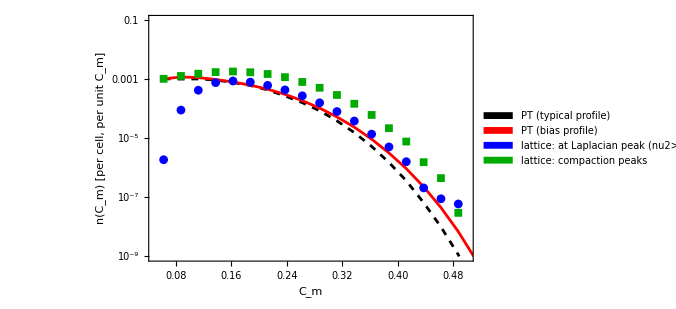

```mathematica
Module[{C=bpU["C"],sel},sel[v_]:=Select[Transpose[{C,v}],#1⟦2⟧>0&];ListLogPlot[{Transpose[{C,bpU["pt0"]}],Transpose[{C,bpU["bias"]}],sel[latUc],sel[latUp]},Joined->{True,True,False,False},PlotStyle->{{Black,Dashed,AbsoluteThickness[2]},{Red,AbsoluteThickness[2]},{Blue,PointSize[0.015]},{Darker[Green],PointSize[0.015]}},PlotMarkers->{None,None,{"●",9},{"■",8}},Frame->True,FrameLabel->{"C_m","n(C_m)  [per cell, per unit C_m]"},PlotRange->{{0.05,0.5},{1/10^9,0.1}},ImageSize->500,PlotLegends->Placed[,Right]]]
```

```mathematica
Module[{C=bpU["C"],rows},rows=Select[Transpose[{C,latUc,latUp,bpU["pt0"],bpU["bias"],latUc/bpU["pt0"],latUc/bpU["bias"],latUp/bpU["pt0"],latUp/bpU["bias"]}],#1⟦2⟧>0&&#1⟦1⟧≥0.1&];Grid[Prepend[N[rows],{"C_m","lat@L-peak","lat C-peak","PT typ.","PT bias","@L/typ","@L/bias","Cpk/typ","Cpk/bias"}],Frame->All]]
```

C_m | lat@L-peak | lat C-peak | PT typ. | PT bias | @L/typ | @L/bias | Cpk/typ | Cpk/bias
0.1125 | 0.00042361 | 0.00153637 | 0.00102242 | 0.00113497 | 0.414323 | 0.373234 | 1.50269 | 1.35366
0.1375 | 0.000766516 | 0.00174215 | 0.000939069 | 0.000982019 | 0.81625 | 0.780551 | 1.85519 | 1.77405
0.1625 | 0.000871569 | 0.00182962 | 0.000775578 | 0.000806651 | 1.12377 | 1.08048 | 2.35904 | 2.26817
0.1875 | 0.000797093 | 0.00172362 | 0.000614183 | 0.000630184 | 1.29781 | 1.26486 | 2.80636 | 2.7351
0.2125 | 0.000618845 | 0.00150514 | 0.000435311 | 0.000460354 | 1.42162 | 1.34428 | 3.45761 | 3.26952
0.2375 | 0.000435054 | 0.00117683 | 0.00027214 | 0.000308386 | 1.59864 | 1.41075 | 4.32438 | 3.81611
0.2625 | 0.00027436 | 0.000807494 | 0.00016076 | 0.00018811 | 1.70665 | 1.45851 | 5.02298 | 4.29267
0.2875 | 0.000158668 | 0.00051415 | 0.0000854815 | 0.000105527 | 1.85616 | 1.50358 | 6.01475 | 4.87223
0.3125 | 0.0000804365 | 0.000292659 | 0.0000389467 | 0.0000528841 | 2.0653 | 1.521 | 7.51434 | 5.53397
0.3375 | 0.0000384152 | 0.000147492 | 0.0000156157 | 0.0000237973 | 2.46004 | 1.61426 | 9.44512 | 6.19782
0.3625 | 0.0000138283 | 0.0000616908 | 5.31373×10^-6 | 9.34528×10^-6 | 2.60237 | 1.47971 | 11.6097 | 6.60128
0.3875 | 5.0962×10^-6 | 0.0000219345 | 1.51864×10^-6 | 3.18253×10^-6 | 3.35577 | 1.60131 | 14.4435 | 6.89217
0.4125 | 1.60933×10^-6 | 7.7486×10^-6 | 3.64×10^-7 | 9.3777×10^-7 | 4.42122 | 1.71612 | 21.2874 | 8.2628
0.4375 | 2.08616×10^-7 | 1.54972×10^-6 | 6.61265×10^-8 | 2.28258×10^-7 | 3.15481 | 0.913949 | 23.4357 | 6.78934
0.4625 | 8.9407×10^-8 | 4.47035×10^-7 | 9.91169×10^-9 | 4.49545×10^-8 | 9.02036 | 1.98883 | 45.1018 | 9.94417
0.4875 | 5.96046×10^-8 | 2.98023×10^-8 | 1.14117×10^-9 | 6.90526×10^-9 | 52.2314 | 8.63178 | 26.1157 | 4.31589

```mathematica
Module[{s2=1/10,kp=π/16,sg,g,f,P13,npk,sig2,edges=Range[2,6,0.5],rows},sg[n_]:=√(Exp[2 n^2 s2] kp^(2 n));g=Exp[-2 s2];f[x_]:=1/2 x (x^2-3) (Erf[1/2 √(5/2) x]+Erf[√(5/2) x])+√(2/(5 π)) ((8/5+(31 x^2)/4) Exp[-(5 x^2)/8]+(-8/5+x^2/2) Exp[-(5 x^2)/2]);P13[nu_,xi_]:=Exp[-1/2 (nu^2+(xi-g nu)^2/(1-g^2))]/(2 π √(1-g^2));npk[nu_,k_]:=(2 (sg[4]/sg[3])^3 nu k f[nu k^2] P13[nu,nu k^2])/(6 π)^(3/2);sig2=sg[2];rows=Table[Module[{a=edges⟦i⟧,b=edges⟦i+1⟧,cnt,pt},cnt=Count[cprofU⟦All,4⟧/sig2,_?(a≤#1<b&)];pt=NIntegrate[npk[nu,k],{nu,a,b},{k,0.01,3}]/(b-a);{(a+b)/2,cnt,cnt/((10. 512^3) (b-a)),pt,cnt/(((10. 512^3) (b-a)) pt)}],{i,Length[edges]-1}];Grid[Prepend[N[rows],{"nu2","count","lattice n","PT n","lattice/PT"}],Frame->All]]
```

nu2 | count | lattice n | PT n | lattice/PT
2.25 | 84823. | 0.000126396 | 0.0000874996 | 1.44453
2.75 | 45342. | 0.0000675648 | 0.000052656 | 1.28314
3.25 | 17335. | 0.0000258312 | 0.0000219927 | 1.17453
3.75 | 4902. | 7.30455×10^-6 | 6.53782×10^-6 | 1.11728
4.25 | 995. | 1.48267×10^-6 | 1.41278×10^-6 | 1.04947
4.75 | 173. | 2.5779×10^-7 | 2.25652×10^-7 | 1.14243
5.25 | 21. | 3.12924×10^-8 | 2.69749×10^-8 | 1.16006
5.75 | 3. | 4.47035×10^-9 | 2.43555×10^-9 | 1.83546

結果 (A_s=1e-2, NL=512, npeak=16)。(1) Laplacian peak 中心の C_m (青丸) に対しては、typical PT は lattice/PT(ν₂≥2 に制限) = 1.2 (C_m=0.16), 1.4 (0.21), 1.7 (0.26), 2.1 (0.31), 2.6 (0.36), 4.5 (0.41) と C_m とともに不足が増えるが、bias-profile PT では lattice/bias-PT = 1.3, 1.4, 1.5, 1.5, 1.5, 1.7 とほぼ一定 (C_m=0.16–0.41) になり、高 C tail の形は再現される。残る 1.3–1.7 倍の定数的な超過は、この設定では lattice の Laplacian peak 数密度が PT より多いこと (ν₂ ビン別 lattice/PT = 1.45 (2.25), 1.28 (2.75), 1.17 (3.25), 1.12 (3.75), 1.05 (4.25)) と概ね同程度である。(2) compaction peak (緑四角) は peak 中心の C_m より更に多く、C_m とともに差が開く: lattice/bias-PT = 2.3 (0.16), 3.3 (0.21), 4.3 (0.26), 5.5 (0.31), 6.6 (0.36), 8.3 (0.41) (typical PT に対しては 2.4, 3.5, 5.0, 7.5, 11.6, 21)。compaction peak / peak 中心の比は 2.4 (0.21), 3.6 (0.31), 4.8 (0.41) で、これは profile 揺らぎではなく、compaction peak が Laplacian peak の中心に限らず (空間位置と半径の最大化、1 つの構造に複数の極大など) 数えられていることによる差である。npeak=32 の設定 (lattice/bias-PT = 3.3 (0.31)) よりも悪化しており、kpeak が小さい (構造が格子上で良く分解される) ほど compaction peak と PT の量の違いが目立つ。